```mathematica
Discrete scale invariance and complex dimensions
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/akapiisp/Documents/research/holographicdiscrete

### Some stuff:

```mathematica
f[x_,A_,k_] = -((2*A*k*Sin[k*x]+6*A*Cos[k*x]+6)/(1+A*Cos[k*x])^2)
```

-(6+6 A Cos[k x]+2 A k Sin[k x])/(1+A Cos[k x])^2

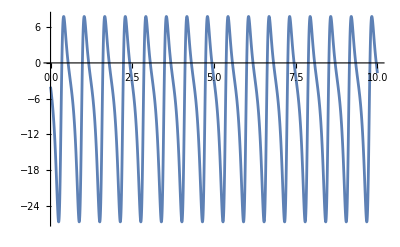

```mathematica
Plot[f[x,0.5,10],{x,0,10}]
```

```mathematica
eom1var= r''[λ]+r'[λ]^2+A*k*Sin[k*z[λ]]/(2*Exp[2*z[λ]]*(1+A*Cos[k*z[λ]]))z'[λ]^2==0;
eom2var = z''[λ]-(A*k*Sin[k*z[λ]])/(2*(1+A*Cos[k*z[λ]]))*z'[λ]^2+1/(1+A*Cos[k*z[λ]])*r'[λ]*z'[λ]==0;
```

```mathematica
eps = 10 ^ -4;
λmin = eps;
λmax = 10000;
eom1 = eom1var /.A->0/.k->4;
eom2 = eom2var/.A->0/.k->4;
sol = NDSolve[{ eom1,eom2,r[eps]==1,z[eps]==eps,r'[eps]==0.1,z'[eps]==0.1},{r,z},{λ,λmin,λmax}]
```

{{r→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

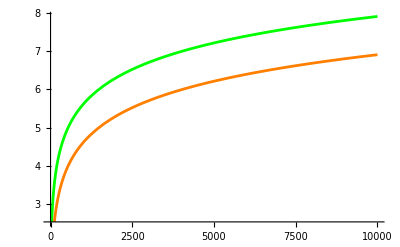

```mathematica
Plot[{r[λ]/.sol,z[λ]/.sol},{λ,λmin,λmax},PlotStyle-> {Green,Orange}]
```

```mathematica
.b4Plot[{r[Tan[x]]/.sol,z[Tan[x]]/.sol},{x,ArcTan[λmin],ArcTan[λmax]},PlotStyle-> {Green,Orange},PlotRange->{0,20}]
```

```mathematica
gzz[z_] = (1+A*Cos[k*z]);
grr[z_] = Exp[-2*z];
gtt = r^2*Exp[-2*z];
```

(*Induced metric*)
(gzz*z'^2 + grr) dr^2

Geodesic length :
int_r0^r1 sqrt{gzz*z’^2 + grr} dr

```mathematica
f[Avar_,kvar_,zbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*z])/(1-Exp[2*(z-zbarvar)])] ,{z,10^(-4),zbarvar}]
```

NIntegrate::nlim: z = zbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar z])/(1-Exp[2 (z-zbarvar)])),{z,1/10^4,zbarvar}]

```mathematica
f[0.1,1,1]
```

3.43993

```mathematica
Plot3D[Exp[-Abs[f[x,1,y]]],{x,0,2},{y,0,10}, AxesLabel -> {"A","zstar"}]
```

-Graphics3D-

```mathematica
Abs[f[0,2,100]]
```

3.14159

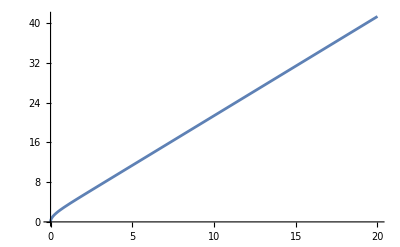

```mathematica
Plot[Abs[f[0,2,y]],{y,0,20}]
```

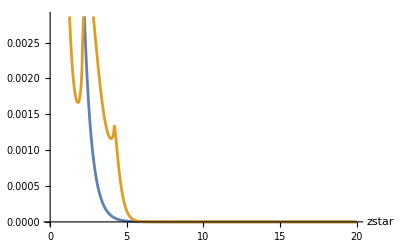

```mathematica
Plot[{Exp[-Abs[f[0,1,y]]],Exp[-Abs[f[2,1,y]]]},{y,0,20}, AxesLabel -> {"zstar"}]
```

```mathematica
gzz[z_] = (1+A*Cos[k*z]);
grr[z_] = Exp[2*z];
gtt = r^2*Exp[2*z];
```

(*Induced metric*)
(gzz*z'^2 + grr) dr^2

Geodesic length :
int_r0^r1 sqrt{gzz*z’^2 + grr} dr

```mathematica
zbarmax = 100;
f[Avar_,kvar_,zbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*z])/(1-Exp[2*(zbarvar-z)])](*-2*Sqrt[Exp[2*zbarvar]*(1+Avar*Cos[kvar*z])/(Exp[2*z]*(Exp[2*z]-Exp[2*zbarvar]))]*) ,{z,zbarvar,zbarmax}]
R[Avar_,kvar_,zbarvar_] = NIntegrate[ 2*Sqrt[Exp[2*zbarvar]*(1+Avar*Cos[kvar*z])/(Exp[2*z]*(Exp[2*z]-Exp[2*zbarvar]))],{z,zbarvar,zbarmax}]
```

NIntegrate::nlim: z = zbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar z])/(1-Exp[2 (zbarvar-z)])),{z,zbarvar,zbarmax}]

NIntegrate::nlim: z = zbarvar is not a valid limit of integration.

NIntegrate[2 √((Exp[2 zbarvar] (1+Avar Cos[kvar z]))/(Exp[2 z] (Exp[2 z]-Exp[2 zbarvar]))),{z,zbarvar,zbarmax}]

```mathematica
f[0.1,1,1]
```

99.2371

```mathematica
Plot3D[Exp[-f[x,1,y]],{x,0,0.8},{y,0,10}, AxesLabel -> {"A","zstar"}]
```

-Graphics3D-

```mathematica
Plot3D[R[x,1,y],{x,0,0.8},{y,0,10}, AxesLabel -> {"A","zstar"}]
```

-Graphics3D-

```mathematica
Plot[2*Sqrt[Exp[2*1]*(1)/(Exp[2*z]*(Exp[2*z]-Exp[2*1]))],{z,0,1}]
```

-Graphics-

```mathematica
lA = Table[i,{i,0,0.9,0.05}];
lz = Table[i,{i,0,2,0.05}];
k=20;
data = {};
For[i=1,i<Dimensions[lA][[1]],i++,
For[j=1,j<Dimensions[lz][[1]],j++,
AppendTo[data,{lA[[i]],R[lA[[i]],k,lz[[j]]],-f[lA[[i]],k,lz[[j]]]}]
]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {70.3109}. NIntegrate obtained 200.648 and 0.000291476 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {66.2263}. NIntegrate obtained 200.486 and 0.000286285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {56.4873}. NIntegrate obtained 200.334 and 0.000288605 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
data
```

```mathematica
ListPlot3D[data,AxesLabel -> {"A","R","Log[corr]"}]
```

-Graphics3D-

```mathematica
Plot3D[-f[x,20,y],{x,0,0.8},{y,0,10}, AxesLabel -> {"A","zstar"}]
```

-Graphics3D-

```mathematica
Plot3D[R[x,20,y],{x,0,0.8},{y,0,10}, AxesLabel -> {"A","zstar"}]
```

-Graphics3D-

```mathematica
lz = Table[i,{i,0,4,0.05}];
k=10;
dat1 = {};
dat2= {};
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{R[0,k,lz[[i]]],-f[0,k,lz[[i]]]}]
]
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{R[0.1,k,lz[[i]]],-f[0.1,k,lz[[i]]]}]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

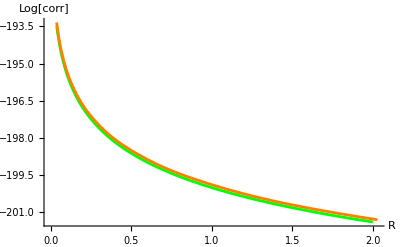

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"R","Log[corr]"}],Plot[-Log[x],{x,1,2}]]
```

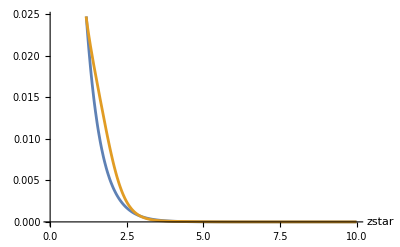

```mathematica
Plot[{Exp[-f[0,2,y]],Exp[-f[0.5,2,y]]},{y,0,10}, AxesLabel -> {"zstar"}]
```

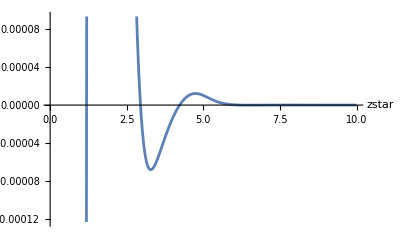

```mathematica
Plot[{Exp[-f[0.5,2,y]]-Exp[-f[0,2,y]]},{y,0,10}, AxesLabel -> {"zstar"}]
```

```mathematica
Ove[Avar_,kvar_] = Integrate[Exp[-f[Avar,kvar,y]]-Exp[-f[0,0,y]],{y,2π/kvar,4π/kvar}]
```

NIntegrate::nlim: z = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

∫_((2 π)/kvar)^((4 π)/kvar) (-ⅇ^(-NIntegrate[2 √((1+0 Cos[0 z])/(1-Exp[2 (z-y)])),{z,1/10^4,y}])+ⅇ^(-NIntegrate[2 √((1+Avar Cos[kvar z])/(1-Exp[2 (z-y)])),{z,1/10^4,y}]))ⅆy

```mathematica
Ove[0.5,1]
```

NIntegrate::nlim: z = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

∫_(2 π)^(4 π) (-ⅇ^(-NIntegrate[2 √((1+0 Cos[0 z])/(1-Exp[2 (z-y)])),{z,1/10^4,y}])+ⅇ^(-NIntegrate[2 √((1+0.5 Cos[1 z])/(1-Exp[2 (z-y)])),{z,1/10^4,y}]))ⅆy

```mathematica
R[Avar_,kvar_,zbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*z])/(1-Exp[2*(zbarvar-z)])] ,{z,10^(-4),zbarvar}]
```

```mathematica
(*Inv coords*)
```

```mathematica
gzz[z_] = (1+A*Cos[k*Log[ϵ]])/ϵ^2;
grr[z_] = 1/ϵ^2;
gtt = r^2/ϵ^2;
```

```mathematica
(*eps = 0.1;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*1/Sqrt[(ϵbarvar/ϵ)^2-1]*(1-ϵ^2)/ϵ^2(*-2*Sqrt[Exp[2*zbarvar]*(1+Avar*Cos[kvar*z])/(Exp[2*z]*(Exp[2*z]-Exp[2*zbarvar]))]*) ,{ϵ,eps,ϵbarvar}]
-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*1/Sqrt[(ϵbarvar/ϵ)^2-1],{ϵ,ϵbarvar,1}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] *)
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]) (1-ϵ^2))/(√((ϵbarvar/ϵ)^2-1) ϵ^2),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(√((ϵbarvar/ϵ)^2-1)),{ϵ,ϵbarvar,1}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

```mathematica
eps = 0.0;
epsmax = 100;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

```mathematica
Integrate[2*1/Sqrt[(ϵbarvar/ϵ)^2-1]*(1-ϵ^2)/ϵ^2,{ϵ,s,ϵbarvar}]
```

$Aborted

```mathematica
f[0.1,1,0.3]
```

4.65134

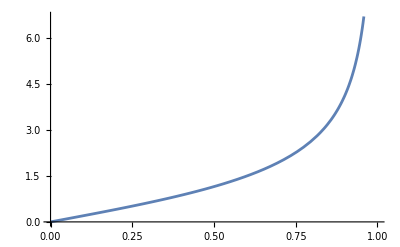

```mathematica
Plot[2*Sqrt[(1+0*Cos[kvar*Log[ϵ]])/((1/ϵ)^2-1)],{ϵ,0,1}]
```

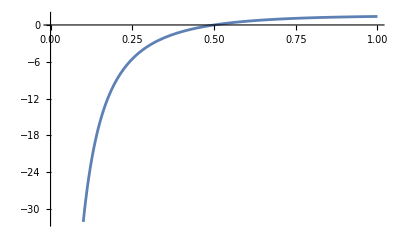

```mathematica
Plot[f[0,0,x],{x,eps,epsmax}]
```

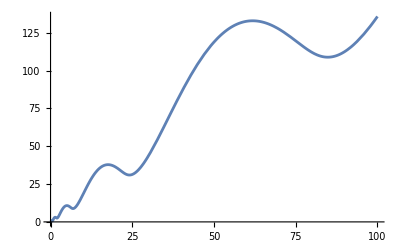

```mathematica
Plot[R[0.9,5,x],{x,eps,epsmax}]
```

```mathematica
Plot3D[f[x,10,y],{x,0,0.9},{y,eps,epsmax}, AxesLabel -> {"A","zstar"}]
```

-Graphics3D-

```mathematica
Plot3D[R[x,10,y],{x,0,0.9},{y,eps,epsmax}, AxesLabel -> {"A","zstar"}]
```

-Graphics3D-

```mathematica
R[0.1,1,2]
```

0.262387

```mathematica
lA = Table[i,{i,0,0.9,0.05}];
lz = Table[i,{i,0,2,0.05}];
k=20;
data = {};
For[i=1,i<Dimensions[lA][[1]],i++,
For[j=1,j<Dimensions[lz][[1]],j++,
AppendTo[data,{lA[[i]],R[lA[[i]],k,lz[[j]]],-f[lA[[i]],k,lz[[j]]]}]
]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {70.3109}. NIntegrate obtained 200.648 and 0.000291476 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {66.2263}. NIntegrate obtained 200.486 and 0.000286285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {56.4873}. NIntegrate obtained 200.334 and 0.000288605 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
data
```

```mathematica
Inverse[R[0,0,lz[[i]]]]
```

```mathematica
eps
```

0.01

```mathematica
lz = Table[i,{i,epsmax/100,epsmax,epsmax/100}];
k=20;
A = 0.9;
dat1 = {};
dat2= {};
dat3 = {};
dat4  ={};
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{R[0,k,lz[[i]]],Exp[-f[0,k,lz[[i]]]]}]
]
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{R[A,k,lz[[i]]],Exp[-f[A,k,lz[[i]]]]}]
]
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat3,{lz[[i]],f[0,k,lz[[i]]]}]
]
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat4,{lz[[i]],f[A,k,lz[[i]]]}]
]
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {1.38151}. NIntegrate obtained 375.132 and 0.000593506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {2.90269}. NIntegrate obtained 1145.4 and 0.0015001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {12.4336}. NIntegrate obtained 3359.41 and 0.00696061 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

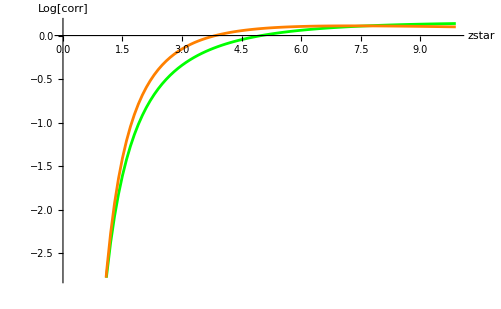

```mathematica
Show[ListLinePlot[{dat3,dat4},PlotStyle-> {Green,Orange},AxesLabel -> {"zstar","Log[corr]"}]]
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,10000}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

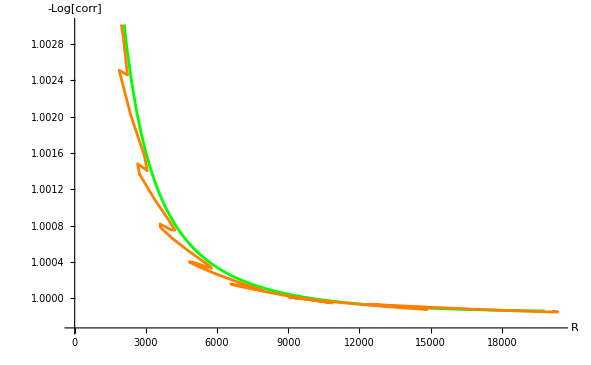

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"R","-Log[corr]"}]]
```

```mathematica
eps = 0.0;
epsmax = 100;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}]
```

```mathematica
zl = epsmax/2;
kt=Table[i,{i,0,20,1}];
A = 0.9;
lA = Table[i,{i,0,A,A/20}];
dat = {};
For[k=1,k<Dimensions[kt][[1]],k++,
dataux = {};
For[j=1,j<Dimensions[lA][[1]],j++,
lz = Table[i,{i,(zl+zl*lA[[j]])/1000,zl+zl*lA[[j]],(zl+zl*lA[[j]])/100}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dataux,{lA[[j]],Log[R[lA[[j]],kt[[k]],lz[[i]]]],Exp[-f[lA[[j]],kt[[k]],lz[[i]]]]}]
];
];
AppendTo[dat,dataux];
Export["dat.mx",dat];
];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.782867}. NIntegrate obtained 141.545 and 0.00374562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.254378}. NIntegrate obtained 176.51 and 0.000304152 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.256624}. NIntegrate obtained 170.478 and 0.000443873 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Dimensions[dat]
```

{20,1980,3}

```mathematica
ListPointPlot3D[dat[[20]],PlotRange->{{0,0.9},{2,4},{1,4}}]
```

-Graphics3D-

```mathematica
Dimensions[Import["dat.mx"]]
```

{20,1980,3}

```mathematica
zl = epsmax/2;
kt=Table[i,{i,0,20,1}];
A = 0.9;
lA = Table[i,{i,0,A,A/20}];
dat2 = {};
For[k=1,k<Dimensions[kt][[1]],k++,
dataux = {};
For[j=1,j<Dimensions[lA][[1]],j++,
lz = Table[i,{i,(zl+zl*lA[[j]])/1000,zl+zl*lA[[j]],(zl+zl*lA[[j]])/100}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dataux,{lA[[j]],Log[R[lA[[j]],kt[[k]],lz[[i]]]],f[lA[[j]],kt[[k]],lz[[i]]]}]
];
];
AppendTo[dat2,dataux];
Export["dat2.mx",dat2];
];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.782867}. NIntegrate obtained 141.545 and 0.00374562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.254378}. NIntegrate obtained 176.51 and 0.000304152 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.256624}. NIntegrate obtained 170.478 and 0.000443873 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
ListPointPlot3D[dat2[[20]],PlotRange->{{0,0.9},{3.5,4},{-0.1,0}}]
```

-Graphics3D-

```mathematica
eps = 0.0;
epsmax = 10000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

```mathematica
zl = epsmax/2;
kt=Table[i,{i,0,20,1}];
A = 1;
lA = Table[i,{i,0,A,A/10}];
datlarge = {};
For[k=1,k<Dimensions[kt][[1]],k++,
dataux = {};
For[j=1,j<Dimensions[lA][[1]],j++,
datauxaux = {};
lz = Table[i,{i,(zl+zl*lA[[j]])/10000,zl+zl*lA[[j]],(zl+zl*lA[[j]])/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[datauxaux,{lA[[j]],Log[R[lA[[j]],kt[[k]],lz[[i]]]],f[lA[[j]],kt[[k]],lz[[i]]]}]
];
AppendTo[dataux,datauxaux];
];
AppendTo[datlarge,dataux];
Export["datlarge.mx",datlarge];
];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {2.32748}. NIntegrate obtained 18.4341 and 0.00121876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {40.3143}. NIntegrate obtained 1.41791 and 2.09036×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {48.7879}. NIntegrate obtained 0.684529 and 8.99872×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
dat = Import["datlarge.mx"];
```

```mathematica
ListPointPlot3D[dat[[1]]]
```

-Graphics3D-

```mathematica
I
```

```mathematica
datcorr = {};
For[k=1, k<= Dimensions[dat][[1]],k++,
datcorraux = {};
For[j=1,j<=Dimensions[dat][[2]],j++,
datcorrauxaux = {};	
For[i=1,i<=Dimensions[dat][[3]],i++,
AppendTo[datcorrauxaux,{dat[[k,j,i]][[1]],dat[[k,j,i]][[2]],Exp[-dat[[k,j,i]][[3]]]}]
];
AppendTo[datcorraux,datcorrauxaux];
];
AppendTo[datcorr,datcorraux];
Export["datcorr.mx",datcorr];
]
```

### Maybe best way:

#### first req:

```mathematica
eps = 0.0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

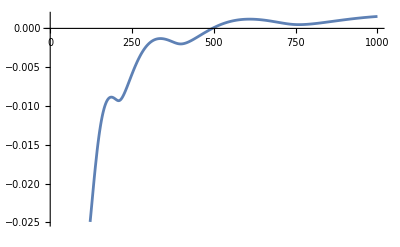

```mathematica
Plot[f[0.9,10,x],{x,1,epsmax}]
```

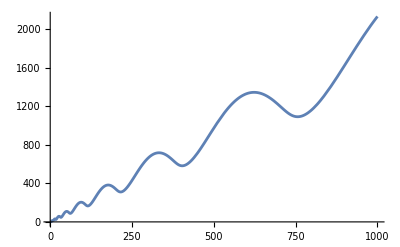

```mathematica
Plot[R[0.9,10,x],{x,1,epsmax}]
```

```mathematica
zl = epsmax/2;
k=10;
A = 0.9;
dat1 = {};
dat2= {};
dat3 = {};
dat4  ={};
norm = √(1+A);

lz = Table[i,{i,(zl+zl*0)/100000,zl+zl*0,(zl+zl*0)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[0,0,lz[[i]]]],Exp[-f[0,0,lz[[i]]]]}]
]
lz = Table[i,{i,(zl+zl*A)/100000,zl+zl*A,(zl+zl*A)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A,k,lz[[i]]]/norm],Exp[-f[A,k,lz[[i]]]/norm]}]
]

lz = Table[i,{i,(zl+zl*0)/10000,zl+zl*0,(zl+zl*0)/100}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat3,{lz[[i]],norm*f[0,0,lz[[i]]]}]
]
lz = Table[i,{i,(zl+zl*A)/10000,zl+zl*A,(zl+zl*A)/100}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat4,{lz[[i]],f[A,k,lz[[i]]]}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.147259}. NIntegrate obtained 2282.21 and 21.211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {9.74732}. NIntegrate obtained 3.85325 and 0.000272342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {10.51970029786728932919004364521242678165435791015625}. NIntegrate obtained 1.70424 and 0.0000122306 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.233182}. NIntegrate obtained 180.804 and 0.0160947 for the integral and error estimates.

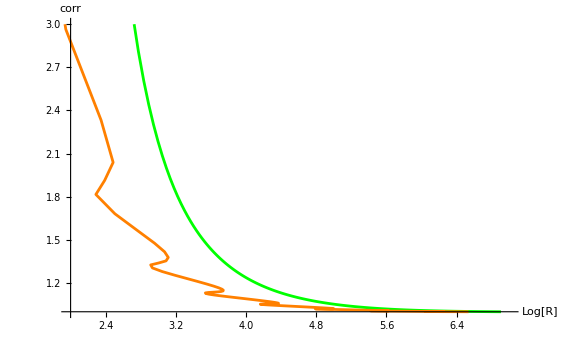

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"Log[R]","corr"},PlotRange->{{2,7},{1,3}}]]
```

Is this signal of effective cutoff?

#### second req:

```mathematica
eps = 0.0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

```mathematica
Plot[f[0.9,10,x],{x,1,epsmax}]
```

-Graphics-

```mathematica
Plot[R[0.9,10,x],{x,1,epsmax}]
```

-Graphics-

```mathematica
k=10;
A = 0.9;
n=-5;
var = Exp[2π*n/k];
Δf =f[0,0,var]- f[A,k,var]
facR = R[0,0,var]/R[A,k,var]

f[A,k,var]
f[0,0,var]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.13413}. NIntegrate obtained 433.775 and 0.0980671 for the integral and error estimates.

-34.9864

0.933811

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.13413}. NIntegrate obtained 433.775 and 0.0980671 for the integral and error estimates.

-398.032

-433.018

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.134131}. NIntegrate obtained 433.764 and 0.0980577 for the integral and error estimates.

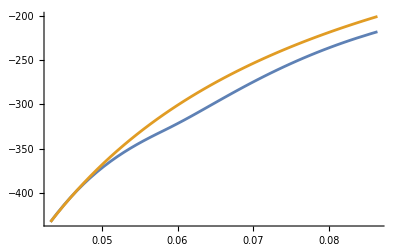

```mathematica
Plot[{f[A,k,x]+Δf,f[0,0,x]},{x,var,var*2}]
```

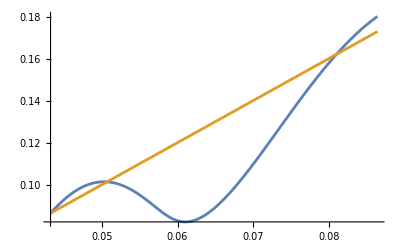

```mathematica
Plot[{R[0.9,10,x]*facR,R[0,0,x]},{x,var,var*2}]
```

```mathematica
zl = epsmax/2;

k=2;
A = 0.05;
n=-1;
var = Exp[2π*n/k];
Δf =f[0,0,var]- f[A,k,var];
facR = R[0,0,var]/R[A,k,var];

dat1 = {};
dat2= {};
dat3 = {};
dat4  ={};

lz = Table[i,{i,var,zl+zl*0,(zl+zl*0)/200}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[0,0,lz[[i]]]],Exp[-f[0,0,lz[[i]]]]}]
]
lz = Table[i,{i,var,zl+zl*A,(zl+zl*A)/200}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A,k,lz[[i]]]*facR],Exp[-(f[A,k,lz[[i]]]+Δf)]}]
]

lz = Table[i,{i,(zl+zl*0)/10000,zl+zl*0,(zl+zl*0)/100}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat3,{lz[[i]],f[0,0,lz[[i]]]}]
]
lz = Table[i,{i,(zl+zl*A)/10000,zl+zl*A,(zl+zl*A)/100}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat4,{lz[[i]],f[A,k,lz[[i]]]+Δf}]
]
```

```mathematica
dat1[[1]]
dat2[[1]]
```

{-2.44845,1.14103×10^188}

{-2.44845,1.14103×10^188}

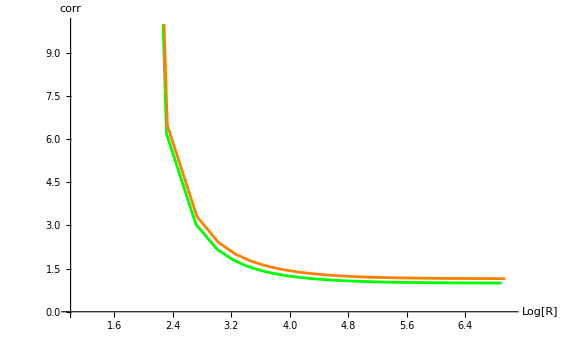

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"Log[R]","corr"},PlotRange->{{1,7},{0,10}}]]
```

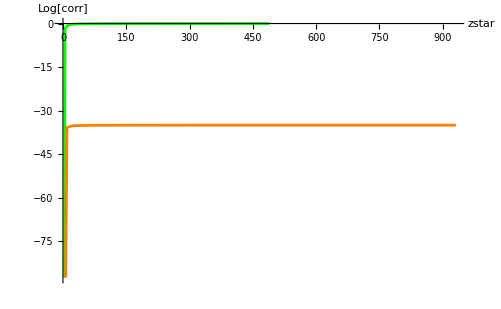

```mathematica
Show[ListLinePlot[{dat3,dat4},PlotStyle-> {Green,Orange},AxesLabel -> {"zstar","Log[corr]"}]]
```

#### third req:

```mathematica
R[A,k,eps]
```

0.

```mathematica
k=4;
A = 0.5;
n=-k;

eps = Exp[2π*n/k];
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-1/(ϵ*ϵbarvar)),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] 

Δf =f[0,0,eps]- f[A,k,eps];
zl = epsmax/2;

dat1 = {};
dat2= {};
dat3 = {};
dat4  ={};

lz = Table[i,{i,eps,zl+zl*0,(zl+zl*0)/200}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[0,0,lz[[i]]]],f[0,0,lz[[i]]]}]
]
lz = Table[i,{i,eps,zl+zl*A,(zl+zl*A)/200}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A,k,lz[[i]]]],(f[A,k,lz[[i]]]+Δf)}]
]

lz = Table[i,{i,(zl+zl*0)/10000,zl+zl*0,(zl+zl*0)/100}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat3,{lz[[i]],f[0,0,lz[[i]]]}]
]
lz = Table[i,{i,(zl+zl*A)/10000,zl+zl*A,(zl+zl*A)/100}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat4,{lz[[i]],f[A,k,lz[[i]]]+Δf}]
]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]]) (1/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-1/(ϵ ϵbarvar)),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0579583}. NIntegrate obtained 13935.4 and 21.5143 for the integral and error estimates.

```mathematica
dat1[[1]]
dat2[[1]]
```

{Indeterminate,-14127.3}

{Indeterminate,-14127.3}

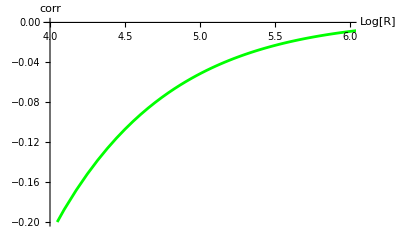

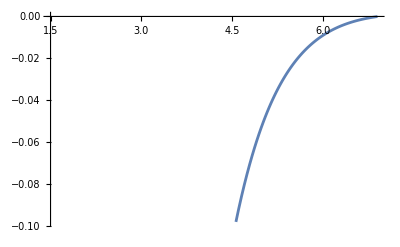

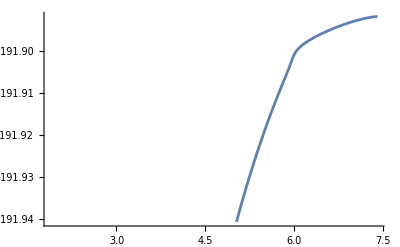

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"Log[R]","corr"},PlotRange->{{4,6},{-0.2,0}}]]
ListLinePlot[dat1]
ListLinePlot[dat2]
```

#### fourth req:

```mathematica
k=10;
A = 0.8;
n=0;
n2=k;
var = Exp[2π*n/k];
var2 =  Exp[2π*n2/k];

eps = 0;
epsmax = 10000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-1/(ϵ*ϵbarvar)),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] 

refR=Log[R[0,0,var]]
reff = f[0,0,var]

refR2=Log[R[0,0,var2]]
reff2 = f[0,0,var2]

Δf =f[0,0,var]- f[A,k,var];
facR = R[0,0,var]/ R[A,k,var];

dat1 = {};
dat2= {};

lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[0,0,lz[[i]]]],f[0,0,lz[[i]]]}]
]
lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A,k,lz[[i]]]*facR],(f[A,k,lz[[i]]]+Δf)}]
]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]]) (1/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-1/(ϵ ϵbarvar)),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

0.693147

-17.0344

6.97633

-0.00834376

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.02919}. NIntegrate obtained 17.4456 and 0.0133214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {32.1535}. NIntegrate obtained 11.0452 and 0.700888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {10.7747}. NIntegrate obtained 6.00716 and 0.00076268 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
dat1[[1]]
dat2[[1]]
```

{0.693147,-17.0344}

{0.693147,-17.0344}

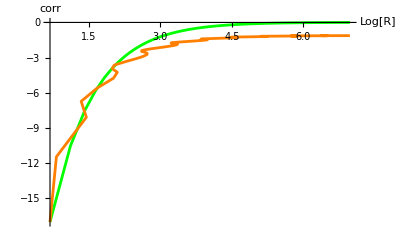

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"Log[R]","corr"},PlotRange->{{refR,refR2},{reff,reff2}}]]
```

```mathematica
k=10;
A = 0.8;
n=-k;
n2=0;
var = Exp[2π*n/k];
var2 =  Exp[2π*n2/k];

eps = 0;
epsmax = 10000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-1/(ϵ*ϵbarvar)),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] 

refR=Log[R[0,0,var]]
reff = f[0,0,var]

refR2=Log[R[0,0,var2]]
reff2 = f[0,0,var2]

Δf =f[0,0,var]- f[A,k,var];
facR = R[0,0,var]/ R[A,k,var];

dat1 = {};
dat2= {};

lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[0,0,lz[[i]]]],f[0,0,lz[[i]]]}]
]
lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A,k,lz[[i]]]*facR],(f[A,k,lz[[i]]]+Δf)}]
]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]]) (1/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-1/(ϵ ϵbarvar)),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

-5.59004

-15851.

0.693147

-17.0344

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0167579}. NIntegrate obtained 15736.8 and 94.8189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0167579}. NIntegrate obtained 15736.8 and 94.8189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0421867}. NIntegrate obtained 9999.11 and 33.3957 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0431848}. NIntegrate obtained 7266.73 and 20.5768 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

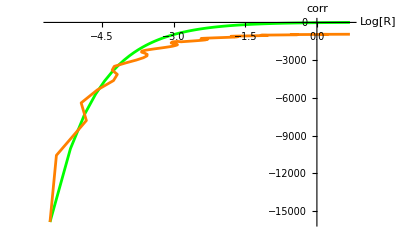

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"Log[R]","corr"},PlotRange->{{refR,refR2},{reff,reff2}}]]
```

```mathematica
k=10;
A = 0.8;
n=k;
n2=2k;
var = Exp[2π*n/k];
var2 =  Exp[2π*n2/k];

eps = 0;
epsmax = 1000000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-1/(ϵ*ϵbarvar)),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] 

refR=Log[R[0,0,var]]
reff = f[0,0,var]

refR2=Log[R[0,0,var2]]
reff2 = f[0,0,var2]

Δf =f[0,0,var]- f[A,k,var];
facR = R[0,0,var]/ R[A,k,var];

dat1 = {};
dat2= {};

lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[0,0,lz[[i]]]],f[0,0,lz[[i]]]}]
]
lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A,k,lz[[i]]]*facR],(f[A,k,lz[[i]]]+Δf)}]
]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]]) (1/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-1/(ϵ ϵbarvar)),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

6.97633

-0.0255435

13.2595

-3.87787×10^-6

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {2912.16}. NIntegrate obtained 0.0267504 and 3.84494×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {2858.65}. NIntegrate obtained 0.0116196 and 9.07001×10^-8 for the integral and error estimates.

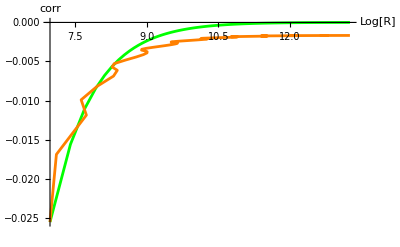

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"Log[R]","corr"},PlotRange->{{refR,refR2},{reff,reff2}}]]
```

#### Fifth req:

```mathematica
k=10;
A = 0.8;
n=0;
n2=k;
var = Exp[2π*n/k];
var2 =  Exp[2π*n2/k];
norm = √(1+A);

eps = 0;
epsmax = 10000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-1/(ϵ*ϵbarvar)),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] 

refR=Log[R[0,0,var]]
reff = f[0,0,var]

refR2=Log[R[0,0,var2]]
reff2 = f[0,0,var2]

Δf =f[0,0,var]- f[A,k,var]/norm;
facR = R[0,0,var]/ (R[A,k,var]/norm);

dat1 = {};
dat2= {};

lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[0,0,lz[[i]]]],f[0,0,lz[[i]]]}]
]
lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A,k,lz[[i]]]/norm*facR],(f[A,k,lz[[i]]]/norm+Δf)}]
]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]]) (1/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-1/(ϵ ϵbarvar)),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

0.693147

-17.0344

6.97633

-0.00834376

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.02919}. NIntegrate obtained 17.4456 and 0.0133214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {32.1535}. NIntegrate obtained 11.0452 and 0.700888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {10.7747}. NIntegrate obtained 6.00716 and 0.00076268 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
dat1[[1]]
dat2[[1]]
```

{0.850227,-14.2897}

{0.850227,-14.2897}

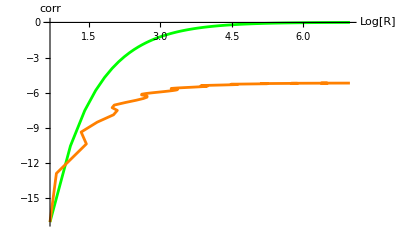

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"Log[R]","corr"},PlotRange->{{refR,refR2},{reff,reff2}}]]
```

#### Sixth req:

```mathematica
k=10;
A = 0.8;
n=0;
n2=k;
var = Exp[2π*n/k];
var2 =  Exp[2π*n2/k];
norm = √(1+A);

eps = 0;
epsmax = 10000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*1/ϵ^2-1/(ϵ*ϵbarvar)),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/(ϵ*ϵbarvar),{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] 

refR=Log[R[0,0,var]]
reff = f[0,0,var]

refR2=Log[R[0,0,var2]]
reff2 = f[0,0,var2]

Δf =f[0,0,var]- f[A,k,var]/norm;
ΔR = R[0,0,var]- (R[A,k,var]/norm);

dat1 = {};
dat2= {};

lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[0,0,lz[[i]]]],f[0,0,lz[[i]]]}]
]
lz = Table[i,{i,var,var2,(var2-var)/1000}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A,k,lz[[i]]]/norm+ΔR],(f[A,k,lz[[i]]]/norm+Δf)}]
]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/(ϵ ϵbarvar),{ϵ,ϵbarvar,epsmax}]+NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]]) (1/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-1/(ϵ ϵbarvar)),{ϵ,eps,ϵbarvar}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

0.693147

-17.0344

6.97633

-0.00834376

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.02919}. NIntegrate obtained 17.4456 and 0.0133214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {32.1535}. NIntegrate obtained 11.0452 and 0.700888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {10.7747}. NIntegrate obtained 6.00716 and 0.00076268 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

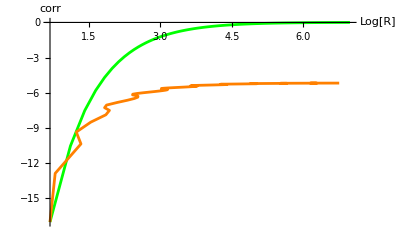

```mathematica
Show[ListLinePlot[{dat1,dat2},PlotStyle-> {Green,Orange},AxesLabel -> {"Log[R]","corr"},PlotRange->{{refR,refR2},{reff,reff2}}]]
```

### Testing:

-(5 (6+6 Avar Cos[kvar r]+Avar kvar Sin[kvar r]))/(1+Avar Cos[kvar r])^2

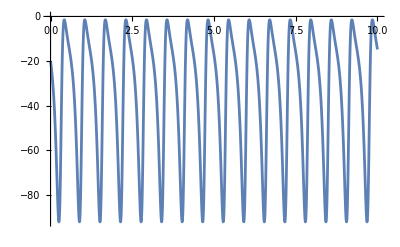

```mathematica
g[Avar_,kvar_,r_] = -(d-1)(d+d*Avar*Cos[kvar*r]+kvar*Avar*Sin[kvar*r])/(1+Avar*Cos[kvar*r])^2/.d->6
Plot[g[0.5,10,r],{r,0,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.00229024}. NIntegrate obtained 36.2002 and 0.678859 for the integral and error estimates.

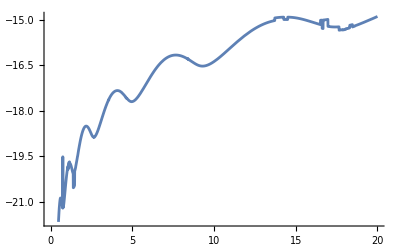

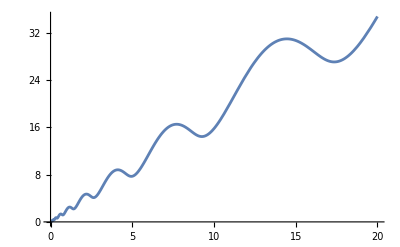

```mathematica
Plot[f[0.9,10,x],{x,0,20}]
Plot[R[0.8,10,x],{x,0,20}]
```

```mathematica
k=9;
A1 = 0.8;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
(*norm = √(1+A);*)
norm = 1;

eps = 0;
epsmax = 100000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] 

refR=Log[R[0,0,var]]
reff = -Log[Abs[f[0,0,var]]]

refR2=Log[R[0,0,var2]]
reff2 = -Log[Abs[f[0,0,var2]]]

Δf1 =-Log[Abs[f[0,0,var]]]+Log[Abs[ f[A1,k,var]]];
ΔR1 =Log[ R[0,0,var]]- Log[R[A1,k,var]];

Δf2 =+f[0,0,var]- f[A1,k,var];
ΔR2 =Log[ R[0,0,var]]- Log[R[A1,k,var]];

Δf3 =+f[0,0,var]-f[A1,k,var];
ΔR3 =R[0,0,var]- R[A1,k,var];


dat0 = {};
dat1 = {};
dat2 = {};
dat3 = {};
dat4 = {};
dat5 = {};


(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat0,{Log[R[0,0,lz[[i]]]],-Log[Abs[f[0,0,lz[[i]]]]]}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[A1,k,lz[[i]]]] + ΔR1,-Log[Abs[(f[A1,k,lz[[i]]])]]+Δf1}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A1,k,lz[[i]]]] + ΔR2,-Log[Abs[f[A1,k,lz[[i]]]+Δf2]]}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat3,{Log[R[A1,k,lz[[i]]]+ ΔR3] ,-Log[Abs[f[A1,k,lz[[i]]]+Δf3]]}]
]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]]) (ϵbarvar/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/ϵ,{ϵ,ϵbarvar,epsmax}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

-5.59004

-3.5324

6.97633

-2.20532

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0482952}. NIntegrate obtained 33.209 and 0.548549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0482952}. NIntegrate obtained 33.209 and 0.548549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0482952}. NIntegrate obtained 33.209 and 0.548549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0482952}. NIntegrate obtained 33.209 and 0.548549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0485453}. NIntegrate obtained 32.8902 and 0.505024 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0488288}. NIntegrate obtained 32.6586 and 0.457378 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0482952}. NIntegrate obtained 33.209 and 0.548549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0485453}. NIntegrate obtained 32.8902 and 0.505024 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0488288}. NIntegrate obtained 32.6586 and 0.457378 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0482952}. NIntegrate obtained 33.209 and 0.548549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0485453}. NIntegrate obtained 32.8902 and 0.505024 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0488288}. NIntegrate obtained 32.6586 and 0.457378 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]]) (ϵbarvar/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/ϵ,{ϵ,ϵbarvar,epsmax}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

0.693147

12.4292

6.97633

-0.137154

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.82418}. NIntegrate obtained 12.0891 and 0.0000178443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.82418}. NIntegrate obtained 11.7784 and 0.000278896 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {13.9997}. NIntegrate obtained 11.4544 and 0.00285206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {14.1447}. NIntegrate obtained 11.3186 and 0.00150879 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.82418}. NIntegrate obtained 11.5421 and 0.00124818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.95299}. NIntegrate obtained 11.3704 and 0.000960887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {13.9997}. NIntegrate obtained 11.2101 and 0.00835326 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.693147,12.4292}

{0.693147,12.4292}

{0.693147,12.4292}

«3 more identical outputs»

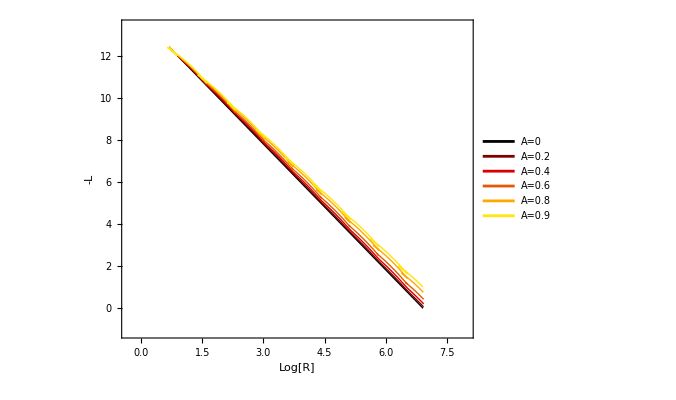

```mathematica
(*R match, L match*)
k=9;
num = 100;
A1= 0.2;
A2 = 0.4;
A3 = 0.6;
A4=0.8;
A5 = 0.9;
n1=0;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
(*norm = √(1+A);*)
norm = 1;

eps = 0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] 

Rref1=Log[R[0,0,var]]
fref1 = -f[0,0,var]

Rref2=Log[R[0,0,var2]]
fref2 =- f[0,0,var2]

Δf1 =+f[0,0,var]-f[A1,k,var];
ΔR1 =R[0,0,var]- R[A1,k,var];

Δf2 =+f[0,0,var]-f[A2,k,var];
ΔR2 =R[0,0,var]- R[A2,k,var];

Δf3 =+f[0,0,var]-f[A3,k,var];
ΔR3 =R[0,0,var]- R[A3,k,var];

Δf4 =+f[0,0,var]-f[A4,k,var];
ΔR4 =R[0,0,var]- R[A4,k,var];

Δf5 =+f[0,0,var]-f[A5,k,var];
ΔR5 =R[0,0,var]- R[A5,k,var];

dat0 = {};
dat1 = {};
dat2 = {};
dat3 = {};
dat4 = {};
dat5 = {};


(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat0,{Log[R[0,0,lz[[i]]]],-f[0,0,lz[[i]]]}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[A1,k,lz[[i]]]+ ΔR1] ,-(f[A1,k,lz[[i]]]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A2,k,lz[[i]]]+ ΔR2] ,-(f[A2,k,lz[[i]]]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat3,{Log[R[A3,k,lz[[i]]]+ ΔR3] ,-(f[A3,k,lz[[i]]]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat4,{Log[R[A4,k,lz[[i]]]+ ΔR4] ,-(f[A4,k,lz[[i]]]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat5,{Log[R[A5,k,lz[[i]]]+ ΔR5] ,-(f[A5,k,lz[[i]]]+Δf5)}]
]

dat0[[1]]
dat1[[1]]
dat2[[1]]
dat3[[1]]
dat4[[1]]
dat5[[1]]


plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->500,AspectRatio->0.8};
Show[ListLinePlot[{dat0,dat1,dat2,dat3,dat4,dat5},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05]},PlotRange->{{Rref1-1,Rref2+1},{fref1+1,fref2-1}},PlotLegends->Placed[{Style["A=0",Black],Style["A=0.2",Black],Style["A=0.4",Black],Style["A=0.6",Black],Style["A=0.8",Black],Style["A=0.9",Black]},{0.20,0.6}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L",Black,28]}]]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]]) (ϵbarvar/(√((ϵbarvar/ϵ)^2-1) ϵ^2)-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]]))/ϵ,{ϵ,ϵbarvar,epsmax}]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]])/((ϵbarvar/ϵ)^2-1)),{ϵ,eps,ϵbarvar}]

0.693147

12.4292

6.97633

-0.137154

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.82418}. NIntegrate obtained 12.0891 and 0.0000178443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.82418}. NIntegrate obtained 11.7784 and 0.000278896 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {13.9997}. NIntegrate obtained 11.4544 and 0.00285206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {14.1447}. NIntegrate obtained 11.3186 and 0.00150879 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.82418}. NIntegrate obtained 11.5421 and 0.00124818 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.95299}. NIntegrate obtained 11.3704 and 0.000960887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {13.9997}. NIntegrate obtained 11.2101 and 0.00835326 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.693147,12.4292}

{0.693147,12.4292}

{0.693147,12.4292}

«3 more identical outputs»

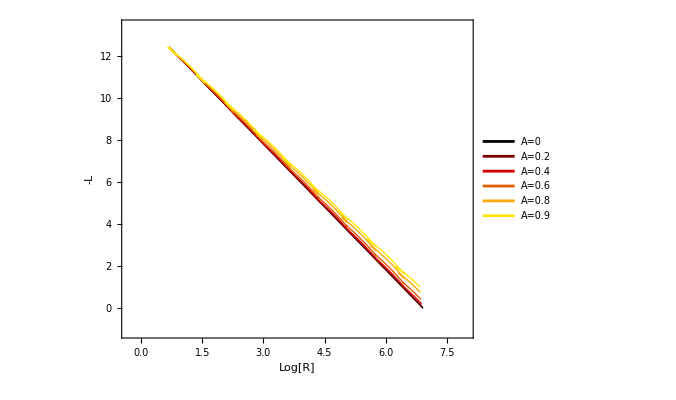

```mathematica
(*Log[R] match, L match*)
k=9;
num = 100;
A1= 0.2;
A2 = 0.4;
A3 = 0.6;
A4=0.8;
A5 = 0.9;
n1=0;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
(*norm = √(1+A);*)
norm = 1;

eps = 0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax}]
R[Avar_,kvar_,ϵbarvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] 

Rref1=Log[R[0,0,var]]
fref1 = -f[0,0,var]

Rref2=Log[R[0,0,var2]]
fref2 =- f[0,0,var2]

Δf1 =+f[0,0,var]-f[A1,k,var];
ΔR1 =Log[R[0,0,var]]-Log[ R[A1,k,var]];

Δf2 =+f[0,0,var]-f[A2,k,var];
ΔR2 =Log[R[0,0,var]]- Log[R[A2,k,var]];

Δf3 =+f[0,0,var]-f[A3,k,var];
ΔR3 =Log[R[0,0,var]]-Log[ R[A3,k,var]];

Δf4 =+f[0,0,var]-f[A4,k,var];
ΔR4 =Log[R[0,0,var]]- Log[R[A4,k,var]];

Δf5 =+f[0,0,var]-f[A5,k,var];
ΔR5 =Log[R[0,0,var]]- Log[R[A5,k,var]];

dat0 = {};
dat1 = {};
dat2 = {};
dat3 = {};
dat4 = {};
dat5 = {};


(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat0,{Log[R[0,0,lz[[i]]]],-f[0,0,lz[[i]]]}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[A1,k,lz[[i]]]]+ ΔR1 ,-(f[A1,k,lz[[i]]]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A2,k,lz[[i]]]]+ ΔR2 ,-(f[A2,k,lz[[i]]]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat3,{Log[R[A3,k,lz[[i]]]]+ ΔR3 ,-(f[A3,k,lz[[i]]]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat4,{Log[R[A4,k,lz[[i]]]]+ ΔR4 ,-(f[A4,k,lz[[i]]]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat5,{Log[R[A5,k,lz[[i]]]]+ ΔR5 ,-(f[A5,k,lz[[i]]]+Δf5)}]
]

dat0[[1]]
dat1[[1]]
dat2[[1]]
dat3[[1]]
dat4[[1]]
dat5[[1]]

plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->500,AspectRatio->0.8};
ListLinePlot[{dat0,dat1,dat2,dat3,dat4,dat5},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05]},PlotRange->{{Rref1-1,Rref2+1},{fref1+1,fref2-1}},PlotLegends->Placed[{Style["A=0",Black],Style["A=0.2",Black],Style["A=0.4",Black],Style["A=0.6",Black],Style["A=0.8",Black],Style["A=0.9",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L",Black,28]}]
```

### Incorporating beta:

```mathematica
g[A_,k_,z_,β_]= -(β (β+A β Cos[k Log[z]]-A k Sin[k Log[z]]))/(2 (1+A Cos[k Log[z]])^2)
```

-(β (β+A β Cos[9 Log[z]]-9 A Sin[9 Log[z]]))/(2 (1+A Cos[9 Log[z]])^2)

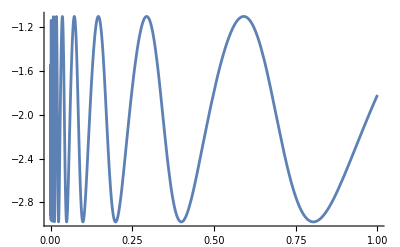

```mathematica
Plot[g[0.1,1,x,2],{x,0,1}]
```

```mathematica
eps = 0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_,βvar_,ϕvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]+ϕvar])]*(1/Sqrt[ϵbarvar^βvar/ϵ^2-1]*ϵbarvar^(βvar/2)/ϵ^(1+βvar/2)-1/ϵ^(βvar/2)),{ϵ,eps,ϵbarvar},AccuracyGoal->2]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]+ϕvar])]/ϵ^(βvar/2),{ϵ,ϵbarvar,epsmax},AccuracyGoal->2]
R[Avar_,kvar_,ϵbarvar_,βvar_,ϕvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]+ϕvar])/(ϵbarvar^βvar/ϵ^2-1)],{ϵ,eps,ϵbarvar},AccuracyGoal->2]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]+ϕvar]))/ϵ^(βvar/2),{ϵ,ϵbarvar,epsmax},AccuracyGoal→2]+NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]+ϕvar]) (ϵbarvar^(βvar/2)/(√(ϵbarvar^βvar/ϵ^2-1) ϵ^(1+βvar/2))-1/ϵ^(βvar/2)),{ϵ,eps,ϵbarvar},AccuracyGoal→2]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]+ϕvar])/(ϵbarvar^βvar/ϵ^2-1)),{ϵ,eps,ϵbarvar},AccuracyGoal→2]

```mathematica
f[0.1,1,0.9,1,0]
f[0.1,1,3,3,0]
f[0.1,1,1,4,0]
```

-34.6038

-1.72005

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {1.56526×10^-57}. NIntegrate obtained 6.88955×10^73 and 6.88955×10^73 for the integral and error estimates.

6.88955×10^73

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0561931}. NIntegrate obtained 77.7133 and 10.3549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0000103723}. NIntegrate obtained -41.0795-48.0394 ⅈ and 3.07879 for the integral and error estimates.

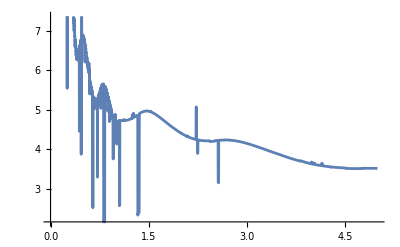

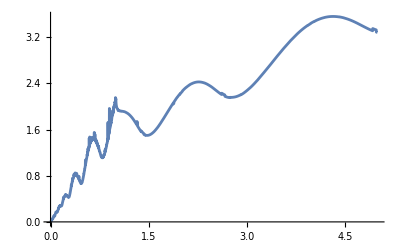

```mathematica
Plot[{Abs[-f[0.9,10,x,2.5,0]]},{x,0,5}]
Plot[{Abs[-R[0.9,10,x,2.5,0]]},{x,0,5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000566421}. NIntegrate obtained 41.2103 and 0.0541137 for the integral and error estimates.

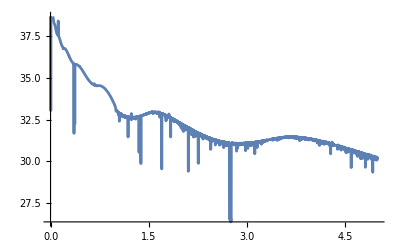

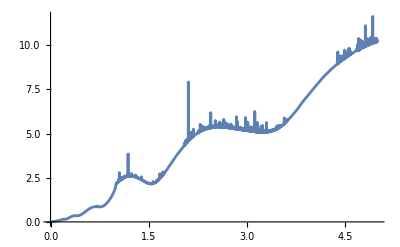

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000566421}. NIntegrate obtained 41.2103 and 0.0541137 for the integral and error estimates.

$Aborted

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000566421}. NIntegrate obtained 41.2103 and 0.0541137 for the integral and error estimates.

$Aborted

$Aborted

$Aborted

```mathematica
Plot[{Re[-f[0.9,10,x,1.5,0]]},{x,0,5}]
Plot[{Im[-f[0.9,10,x,1.5,0]]},{x,0,5}]
Plot[{Re[-R[0.9,10,x,1.5,0]]},{x,0,5}]
Plot[{Im[-R[0.9,10,x,1.5,0]]},{x,0,5}]
```

```mathematica
Plot[{Abs[Exp[-f[0.1,10,Abs[x],1,0]]],Abs[Exp[-f[0.1,10,Abs[x],2,0]]],Abs[Exp[-f[0.1,10,Abs[x],3,0]]]},{x,-1,0.2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.99995749896895720698752484285887209836118927341885864734649658203}. NIntegrate obtained 1.62729-0.00886295 ⅈ and 0.00428051 for the integral and error estimates.

```mathematica
Plot[-R[0.8,10,x,2,0],{x,0,1}]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Re[-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]+ϕvar]))/ϵ^(βvar/2),{ϵ,ϵbarvar,epsmax},AccuracyGoal→2]+NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]+ϕvar]) (ϵbarvar^(βvar/2)/(√(ϵbarvar^βvar/ϵ^2-1) ϵ^(1+βvar/2))-1/ϵ^(βvar/2)),{ϵ,eps,ϵbarvar},AccuracyGoal→2]]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]+ϕvar])/(ϵbarvar^βvar/ϵ^2-1)),{ϵ,eps,ϵbarvar},AccuracyGoal→2]

-5.63526

24.9956

0.693147

12.4292

{-5.63526,24.9956}

{-5.63526,24.9956}

{-5.63526,24.9956}

«1 more identical outputs»

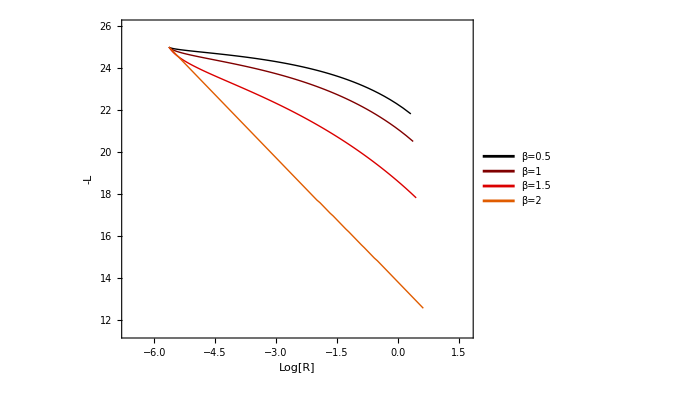

```mathematica
k=9;
A1 = 0;
β1 = 0.5;
β2 = 1;
β3 = 1.5;
β4 = 2;
n1=-k;
n2=0;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
(*norm = √(1+A);*)
norm = 1;

eps = 0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_,βvar_,ϕvar_]=Re[NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]+ϕvar])]*(1/Sqrt[ϵbarvar^βvar/ϵ^2-1]*ϵbarvar^(βvar/2)/ϵ^(1+βvar/2)-1/ϵ^(βvar/2)),{ϵ,eps,ϵbarvar},AccuracyGoal->2]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]+ϕvar])]/ϵ^(βvar/2),{ϵ,ϵbarvar,epsmax},AccuracyGoal->2]]
R[Avar_,kvar_,ϵbarvar_,βvar_,ϕvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]+ϕvar])/(ϵbarvar^βvar/ϵ^2-1)],{ϵ,eps,ϵbarvar},AccuracyGoal->2] 

Rref1=Log[R[A1,k,var,β4,0]]
fref1 = -f[A1,k,var,β4,0]

Rref2=Log[R[A1,k,var2,β4,0]]
fref2 =- f[A1,k,var2,β4,0]

Δf1 =+f[A1,k,var,β4,0]-f[A1,k,var,β1,0];
ΔR1 =R[A1,k,var,β4,0]- R[A1,k,var,β1,0];

Δf2 =+f[A1,k,var,β4,0]-f[A1,k,var,β2,0];
ΔR2 =R[A1,k,var,β4,0]- R[A1,k,var,β2,0];

Δf3 =+f[A1,k,var,β4,0]-f[A1,k,var,β3,0];
ΔR3 =R[A1,k,var,β4,0]- R[A1,k,var,β3,0];

Δf4 =+f[A1,k,var,β4,0]-f[A1,k,var,β4,0];
ΔR4 =R[A1,k,var,β4,0]- R[A1,k,var,β4,0];


dat0 = {};
dat1 = {};
dat2 = {};
dat3 = {};



(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat0,{Log[R[A1,k,lz[[i]],β1,0]+ ΔR1] ,-(f[A1,k,lz[[i]],β1,0]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[A1,k,lz[[i]],β2,0]+ ΔR2] ,-(f[A1,k,lz[[i]],β2,0]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A1,k,lz[[i]],β3,0]+ ΔR3] ,-(f[A1,k,lz[[i]],β3,0]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat3,{Log[R[A1,k,lz[[i]],β4,0]+ ΔR4] ,-(f[A1,k,lz[[i]],β4,0]+Δf4)}]
]

dat0[[1]]
dat1[[1]]
dat2[[1]]
dat3[[1]]

plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->500,AspectRatio->0.8};
ListLinePlot[{dat0,dat1,dat2,dat3},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05]},PlotRange->{{Rref1-1,Rref2+1},{fref1+1,fref2-1}},PlotLegends->Placed[{Style["β=0.5",Black],Style["β=1",Black],Style["β=1.5",Black],Style["β=2",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L",Black,28]}]
```

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Re[-NIntegrate[(2 √(1+Avar Cos[kvar Log[ϵ]+ϕvar]))/ϵ^(βvar/2),{ϵ,ϵbarvar,epsmax},AccuracyGoal→2]+NIntegrate[2 √(1+Avar Cos[kvar Log[ϵ]+ϕvar]) (ϵbarvar^(βvar/2)/(√(ϵbarvar^βvar/ϵ^2-1) ϵ^(1+βvar/2))-1/ϵ^(βvar/2)),{ϵ,eps,ϵbarvar},AccuracyGoal→2]]

NIntegrate::nlim: ϵ = ϵbarvar is not a valid limit of integration.

Re[NIntegrate[2 √((1+Avar Cos[kvar Log[ϵ]+ϕvar])/(ϵbarvar^βvar/ϵ^2-1)),{ϵ,eps,ϵbarvar},AccuracyGoal→2]]

-5.63526

24.9956

0.693147

12.4292

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {2.92304×10^-60}. NIntegrate obtained -2.49641×10^72-270.461 ⅈ and 2.49641×10^72 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000390237}. NIntegrate obtained -8.20411-17.4317 ⅈ and 0.498132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {3.11259×10^-60}. NIntegrate obtained -1.08636×10^186-4472.62 ⅈ and 1.0708×10^186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {3.31444×10^-60}. NIntegrate obtained -1.03635×10^186-4715.71 ⅈ and 1.02151×10^186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {3.52937×10^-60}. NIntegrate obtained -9.88649×10^185-5074.23 ⅈ and 9.7449×10^185 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {2.92304×10^-60}. NIntegrate obtained -2.49641×10^72-270.461 ⅈ and 2.49641×10^72 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0000890435}. NIntegrate obtained -167.073-247.877 ⅈ and 12.4802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {3.52937×10^-60}. NIntegrate obtained 5.00889×10^71-200.379 ⅈ and 5.00889×10^71 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000390237}. NIntegrate obtained -8.20411-17.4317 ⅈ and 0.498132 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000423311}. NIntegrate obtained -8.04233-18.2925 ⅈ and 1.33416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000454898}. NIntegrate obtained -7.56488-16.7242 ⅈ and 0.408461 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

{-5.63526,24.9956}

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

{-5.63526,0.}

{-5.63526,24.9956}

{-5.63526,24.9956}

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {4.26148×10^-60}. NIntegrate obtained -8.58312×10^185-2867.77 ⅈ and 8.46019×10^185 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {4.7276×10^-32}. NIntegrate obtained -9.43471×10^174-3019.96 ⅈ and 9.43471×10^174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {5.83442×10^-60}. NIntegrate obtained -6.78136×10^185-2105.39 ⅈ and 6.68424×10^185 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

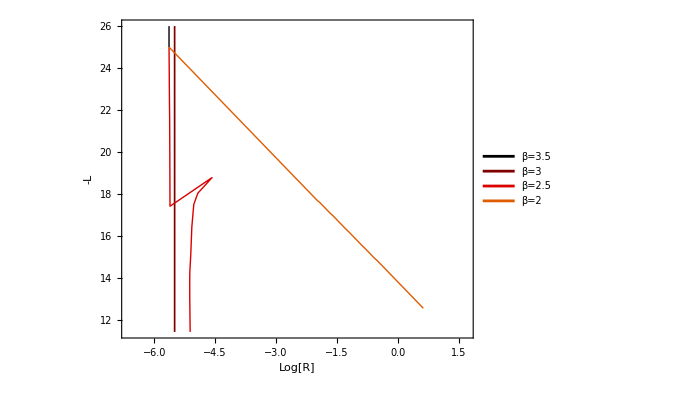

```mathematica
k=10;
num=100;
A1 = 0;
β1 = 3.5;
β2 = 3;
β3 = 2.5;
β4 = 2;
n1=-k;
n2 = 0;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
(*norm = √(1+A);*)
norm = 1;

eps = 0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_,βvar_,ϕvar_]=NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]+ϕvar])]*(1/Sqrt[ϵbarvar^βvar/ϵ^2-1]*ϵbarvar^(βvar/2)/ϵ^(1+βvar/2)-1/ϵ^(βvar/2)),{ϵ,eps,ϵbarvar},AccuracyGoal->2]-NIntegrate[2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]+ϕvar])]/ϵ^(βvar/2),{ϵ,ϵbarvar,epsmax},AccuracyGoal->2]
R[Avar_,kvar_,ϵbarvar_,βvar_,ϕvar_] = NIntegrate[ 2*Sqrt[(1+Avar*Cos[kvar*Log[ϵ]+ϕvar])/(ϵbarvar^βvar/ϵ^2-1)],{ϵ,eps,ϵbarvar},AccuracyGoal->2] 

Rref1=Log[R[A1,k,var,β4,0]]
fref1 = -f[A1,k,var,β4,0]

Rref2=Log[R[A1,k,var2,β4,0]]
fref2 =- f[A1,k,var2,β4,0]

Δf1 =+f[A1,k,var,β4,0]-f[A1,k,var,β1,0];
ΔR1 =R[A1,k,var,β4,0]- R[A1,k,var,β1,0];

Δf2 =+f[A1,k,var,β4,0]-f[A1,k,var,β2,0];
ΔR2 =R[A1,k,var,β4,0]- R[A1,k,var,β2,0];

Δf3 =+f[A1,k,var,β4,0]-f[A1,k,var,β3,0];
ΔR3 =R[A1,k,var,β4,0]- R[A1,k,var,β3,0];

Δf4 =+f[A1,k,var,β4,0]-f[A1,k,var,β4,0];
ΔR4 =R[A1,k,var,β4,0]- R[A1,k,var,β4,0];


dat0 = {};
dat1 = {};
dat2 = {};
dat3 = {};



(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat0,{Log[R[A1,k,lz[[i]],β1,0]+ ΔR1] ,-(f[A1,k,lz[[i]],β1,0]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat1,{Log[R[A1,k,lz[[i]],β2,0]+ ΔR2] ,-(f[A1,k,lz[[i]],β2,0]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat2,{Log[R[A1,k,lz[[i]],β3,0]+ ΔR3] ,-(f[A1,k,lz[[i]],β3,0]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat3,{Log[R[A1,k,lz[[i]],β4,0]+ ΔR4] ,-(f[A1,k,lz[[i]],β4,0]+Δf4)}]
]

dat0[[1]]
dat1[[1]]
dat2[[1]]
dat3[[1]]

plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->500,AspectRatio->0.8};
ListLinePlot[{dat0,dat1,dat2,dat3},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05]},PlotRange->{{Rref1-1,Rref2+1},{fref1+1,fref2-1}},PlotLegends->Placed[{Style["β=3.5",Black],Style["β=3",Black],Style["β=2.5",Black],Style["β=2",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L",Black,28]}]
```

### I should be able introduce beta in this way:

#### R match, L match

```mathematica
(*R match, L match*)
```

```mathematica
N[Exp[2π*n2/k]]
```

535.492

```mathematica
R[0.6,1,10000,4]
```

18408.2

```mathematica
k=1;
num = 200;
β0 = 0.5;
β1 =1;
β2=1.5;
β3=2;
β4=2.5;
β5=3;
β6=3.5;
n0 = -2k;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[Avar_] := 1/√(1);

eps =   0;
epsmax = 10000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=Re[(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar},Method->"LocalAdaptive"]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax},Method->"LocalAdaptive"])/norm[Avar]]
R[Avar_,kvar_,ϵbarvar_,βvar_] := Re[(NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar},Method->"LocalAdaptive"])/norm[Avar]]

Rref1=Log[R[0,k,var^(β3/2),β3]]
fref1 = -f[0,k,var^(β3/2),β3]

Rref2=Log[R[0,k,var2^(β3/2),β3]]
fref2 =- f[0,k,var2^(β3/2),β3]

Δf0 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β0/2),β0];
ΔR0 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β0/2),β0];

Δf1 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β1/2),β1];
ΔR1 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β1/2),β1];

Δf2 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β2/2),β2];
ΔR2 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β2/2),β2];

Δf3 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β3/2),β3];
ΔR3 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β3/2),β3];

Δf4 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β4/2),β4];
ΔR4 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β4/2),β4];

Δf5 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β5/2),β5];
ΔR5 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β5/2),β5];

Δf6 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β6/2),β6];
ΔR6 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β6/2),β6];

dat00 = {};
dat10 = {};
dat20 = {};
dat30 = {};
dat40 = {};
dat50 = {};
dat60 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat00,{Log[R[0,k,lz[[i]]^(β0/2),β0]+ ΔR0],-(f[0,k,lz[[i]]^(β0/2),β0]+Δf0)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat10,{Log[R[0,k,lz[[i]]^(β1/2),β1]+ ΔR1] ,-(f[0,k,lz[[i]]^(β1/2),β1]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat20,{Log[R[0,k,lz[[i]]^(β2/2),β2]+ ΔR2] ,-(f[0,k,lz[[i]]^(β2/2),β2]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat30,{Log[R[0,k,lz[[i]]^(β3/2),β3]+ ΔR3] ,-(f[0,k,lz[[i]]^(β3/2),β3]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat40,{Log[R[0,k,lz[[i]]^(β4/2),β4]+ ΔR4] ,-(f[0,k,lz[[i]]^(β4/2),β4]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat50,{Log[R[0,k,lz[[i]]^(β5/2),β5]+ ΔR5] ,-(f[0,k,lz[[i]]^(β5/2),β5]+Δf5)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat60,{Log[R[0,k,lz[[i]]^(β6/2),β6]+ ΔR6] ,-(f[0,k,lz[[i]]^(β6/2),β6]+Δf6)}]
]
```

-5.59004

29.6007

6.97633

4.46802

```mathematica
k=1;
num = 200;
β0 = 0.5;
β1 =1;
β2=1.5;
β3=2;
β4=2.5;
β5=3;
β6=3.5;
A = 0.6;
n0 = -2k;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[A_] := 1/√(1);

eps =   0;
epsmax = 10000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=Re[(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar},Method->"LocalAdaptive"]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax},Method->"LocalAdaptive"])/norm[Avar]]
R[Avar_,kvar_,ϵbarvar_,βvar_] := Re[(NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar},Method->"LocalAdaptive"])/norm[Avar]]

Δf0 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β0/2),β0];
ΔR0 =R[0,k,var^(β3/2),β3]- R[A,k,var^(β0/2),β0];

Δf1 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β1/2),β1];
ΔR1 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β1/2),β1];

Δf2 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β2/2),β2];
ΔR2 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β2/2),β2];

Δf3 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β3/2),β3];
ΔR3 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β3/2),β3];

Δf4 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β4/2),β4];
ΔR4 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β4/2),β4];

Δf5 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β5/2),β5];
ΔR5 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β5/2),β5];

Δf6 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β6/2),β6];
ΔR6 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β6/2),β6];

dat01= {};
dat11 = {};
dat21 = {};
dat31 = {};
dat41 = {};
dat51 = {};
dat61 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat01,{Log[R[A,k,lz[[i]]^(β0/2),β0]+ ΔR0],-(f[A,k,lz[[i]]^(β0/2),β0]+Δf0)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat11,{Log[R[A,k,lz[[i]]^(β1/2),β1]+ ΔR1] ,-(f[A,k,lz[[i]]^(β1/2),β1]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat21,{Log[R[A,k,lz[[i]]^(β2/2),β2]+ ΔR2] ,-(f[A,k,lz[[i]]^(β2/2),β2]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat31,{Log[R[A,k,lz[[i]]^(β3/2),β3]+ ΔR3] ,-(f[A,k,lz[[i]]^(β3/2),β3]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat41,{Log[R[A,k,lz[[i]]^(β4/2),β4]+ ΔR4] ,-(f[A,k,lz[[i]]^(β4/2),β4]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat51,{Log[R[A,k,lz[[i]]^(β5/2),β5]+ ΔR5] ,-(f[A,k,lz[[i]]^(β5/2),β5]+Δf5)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat61,{Log[R[A,k,lz[[i]]^(β6/2),β6]+ ΔR6] ,-(f[A,k,lz[[i]]^(β6/2),β6]+Δf6)}]
]
```

```mathematica
dat00[[1]]
dat10[[1]]
dat20[[1]]
dat30[[1]]
dat40[[1]]
dat50[[1]]
dat60[[1]]
dat01[[1]]
dat11[[1]]
dat21[[1]]
dat31[[1]]
dat41[[1]]
dat51[[1]]
dat61[[1]]
```

{-5.59004,29.6007}

{-5.59004,29.6007}

{-5.59004,29.6007}

«11 more identical outputs»

```mathematica
Subscript[-L,reg]
```

-L_reg

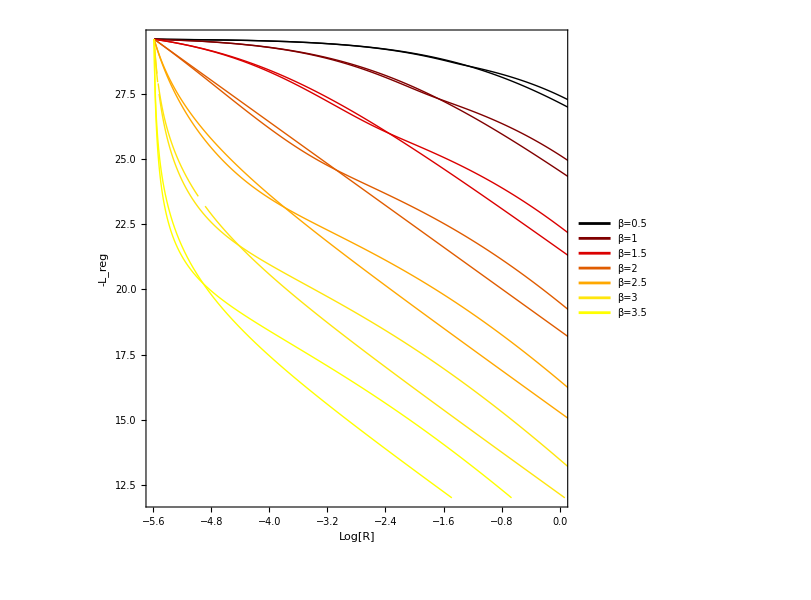

```mathematica
plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->600,AspectRatio->1};
ListLinePlot[{dat00,dat10,dat20,dat30,dat40,dat50,dat60,dat01,dat11,dat21,dat31,dat41,dat51,dat61},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05],RGBColor[1,1,0]},PlotRange->{{Rref1,0},{fref1,12}},PlotLegends->Placed[{Style["β=0.5",Black],Style["β=1",Black],Style["β=1.5",Black],Style["β=2",Black],Style["β=2.5",Black],Style["β=3",Black],Style["β=3.5",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L_reg",Black,28]}]
```

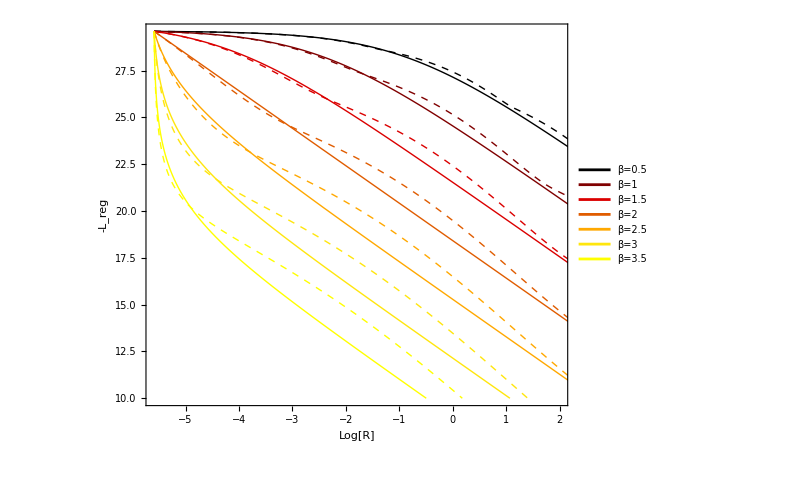

```mathematica
plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->600,AspectRatio->0.8};
ListLinePlot[{dat00,dat10,dat20,dat30,dat40,dat50,dat60,dat01,dat11,dat21,dat31,dat41,dat51,dat61},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05],RGBColor[1,1,0],{RGBColor[0,0,0],Dashed},{RGBColor[0.5,0,0],Dashed},{RGBColor[0.86,0,0],Dashed},{RGBColor[0.88,0.36,0],Dashed},{RGBColor[1,0.66,0],Dashed},{RGBColor[1,0.9,0.05],Dashed},{RGBColor[1,1,0],Dashed}},PlotRange->{{Rref1,2},{fref1,10}},PlotLegends->Placed[{Style["β=0.5",Black],Style["β=1",Black],Style["β=1.5",Black],Style["β=2",Black],Style["β=2.5",Black],Style["β=3",Black],Style["β=3.5",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L_reg",Black,28]}]
```

```mathematica
k=5;
num = 200;
β0 = 0.5;
β1 =1;
β2=1.5;
β3=2;
β4=2.5;
β5=3;
β6=3.5;
n0= -2k;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[Avar_] := 1/√(1);

eps =   0;
epsmax = 10000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=Re[(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar},Method->"LocalAdaptive"]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax},Method->"LocalAdaptive"])/norm[Avar]]
R[Avar_,kvar_,ϵbarvar_,βvar_] := Re[(NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar},Method->"LocalAdaptive"])/norm[Avar]]

Rref1=Log[R[0,k,var^(β3/2),β3]]
fref1 = -f[0,k,var^(β3/2),β3]

Rref2=Log[R[0,k,var2^(β3/2),β3]]
fref2 =- f[0,k,var2^(β3/2),β3]

Δf0 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β0/2),β0];
ΔR0 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β0/2),β0];

Δf1 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β1/2),β1];
ΔR1 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β1/2),β1];

Δf2 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β2/2),β2];
ΔR2 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β2/2),β2];

Δf3 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β3/2),β3];
ΔR3 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β3/2),β3];

Δf4 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β4/2),β4];
ΔR4 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β4/2),β4];

Δf5 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β5/2),β5];
ΔR5 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β5/2),β5];

Δf6 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β6/2),β6];
ΔR6 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β6/2),β6];

dat00 = {};
dat10 = {};
dat20 = {};
dat30 = {};
dat40 = {};
dat50 = {};
dat60 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat00,{Log[R[0,k,lz[[i]]^(β0/2),β0]+ ΔR0],-(f[0,k,lz[[i]]^(β0/2),β0]+Δf0)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat10,{Log[R[0,k,lz[[i]]^(β1/2),β1]+ ΔR1] ,-(f[0,k,lz[[i]]^(β1/2),β1]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat20,{Log[R[0,k,lz[[i]]^(β2/2),β2]+ ΔR2] ,-(f[0,k,lz[[i]]^(β2/2),β2]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat30,{Log[R[0,k,lz[[i]]^(β3/2),β3]+ ΔR3] ,-(f[0,k,lz[[i]]^(β3/2),β3]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat40,{Log[R[0,k,lz[[i]]^(β4/2),β4]+ ΔR4] ,-(f[0,k,lz[[i]]^(β4/2),β4]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat50,{Log[R[0,k,lz[[i]]^(β5/2),β5]+ ΔR5] ,-(f[0,k,lz[[i]]^(β5/2),β5]+Δf5)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat60,{Log[R[0,k,lz[[i]]^(β6/2),β6]+ ΔR6] ,-(f[0,k,lz[[i]]^(β6/2),β6]+Δf6)}]
]
```

-5.59004

29.6007

6.97633

4.46802

```mathematica
k=5;
num = 200;
β0 = 0.5;
β1 =1;
β2=1.5;
β3=2;
β4=2.5;
β5=3;
β6=3.5;
A = 0.6;
n0 = -2k;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[A_] := 1/√(1);

eps =   0;
epsmax = 10000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=Re[(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar},Method->"LocalAdaptive"]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax},Method->"LocalAdaptive"])/norm[Avar]]
R[Avar_,kvar_,ϵbarvar_,βvar_] := Re[(NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar},Method->"LocalAdaptive"])/norm[Avar]]

Δf0 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β0/2),β0];
ΔR0 =R[0,k,var^(β3/2),β3]- R[A,k,var^(β0/2),β0];

Δf1 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β1/2),β1];
ΔR1 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β1/2),β1];

Δf2 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β2/2),β2];
ΔR2 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β2/2),β2];

Δf3 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β3/2),β3];
ΔR3 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β3/2),β3];

Δf4 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β4/2),β4];
ΔR4 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β4/2),β4];

Δf5 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β5/2),β5];
ΔR5 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β5/2),β5];

Δf6 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β6/2),β6];
ΔR6 =+R[0,k,var^(β3/2),β3]- R[A,k,var^(β6/2),β6];

dat01= {};
dat11 = {};
dat21 = {};
dat31 = {};
dat41 = {};
dat51 = {};
dat61 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat01,{Log[R[A,k,lz[[i]]^(β0/2),β0]+ ΔR0],-(f[A,k,lz[[i]]^(β0/2),β0]+Δf0)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat11,{Log[R[A,k,lz[[i]]^(β1/2),β1]+ ΔR1] ,-(f[A,k,lz[[i]]^(β1/2),β1]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat21,{Log[R[A,k,lz[[i]]^(β2/2),β2]+ ΔR2] ,-(f[A,k,lz[[i]]^(β2/2),β2]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat31,{Log[R[A,k,lz[[i]]^(β3/2),β3]+ ΔR3] ,-(f[A,k,lz[[i]]^(β3/2),β3]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat41,{Log[R[A,k,lz[[i]]^(β4/2),β4]+ ΔR4] ,-(f[A,k,lz[[i]]^(β4/2),β4]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat51,{Log[R[A,k,lz[[i]]^(β5/2),β5]+ ΔR5] ,-(f[A,k,lz[[i]]^(β5/2),β5]+Δf5)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat61,{Log[R[A,k,lz[[i]]^(β6/2),β6]+ ΔR6] ,-(f[A,k,lz[[i]]^(β6/2),β6]+Δf6)}]
]
```

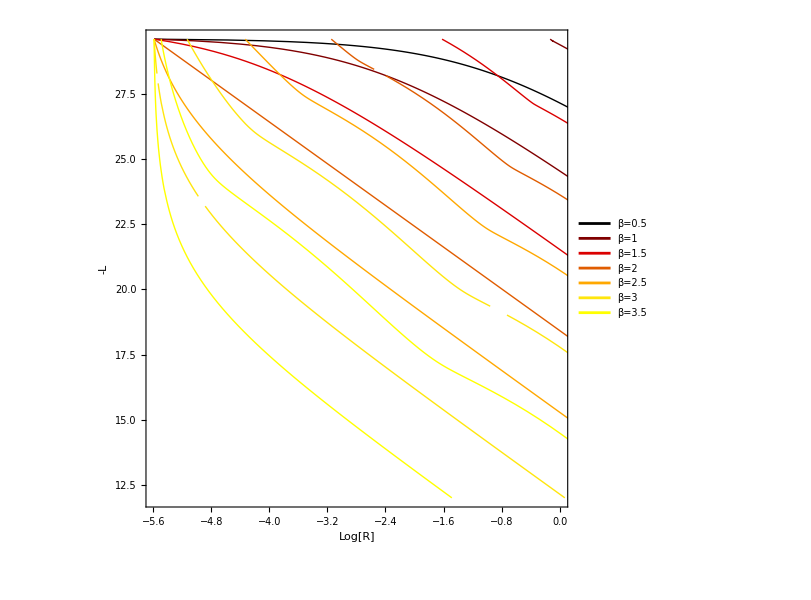

```mathematica
plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->600,AspectRatio->1};
ListLinePlot[{dat00,dat10,dat20,dat30,dat40,dat50,dat60,dat01,dat11,dat21,dat31,dat41,dat51,dat61},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05],RGBColor[1,1,0]},PlotRange->{{Rref1,0},{fref1,12}},PlotLegends->Placed[{Style["β=0.5",Black],Style["β=1",Black],Style["β=1.5",Black],Style["β=2",Black],Style["β=2.5",Black],Style["β=3",Black],Style["β=3.5",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L",Black,28]}]
```

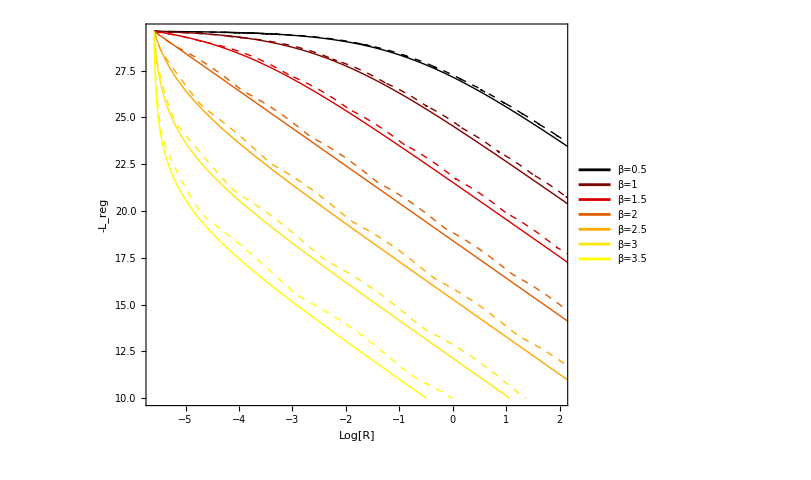

```mathematica
plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->600,AspectRatio->0.8};
ListLinePlot[{dat00,dat10,dat20,dat30,dat40,dat50,dat60,dat01,dat11,dat21,dat31,dat41,dat51,dat61},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05],RGBColor[1,1,0],{RGBColor[0,0,0],Dashed},{RGBColor[0.5,0,0],Dashed},{RGBColor[0.86,0,0],Dashed},{RGBColor[0.88,0.36,0],Dashed},{RGBColor[1,0.66,0],Dashed},{RGBColor[1,0.9,0.05],Dashed},{RGBColor[1,1,0],Dashed}},PlotRange->{{Rref1,2},{fref1,10}},PlotLegends->Placed[{Style["β=0.5",Black],Style["β=1",Black],Style["β=1.5",Black],Style["β=2",Black],Style["β=2.5",Black],Style["β=3",Black],Style["β=3.5",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L_reg",Black,28]}]
```

```mathematica
k=1;
num = 200;
β0 = 0.25;
β1 =0.5;
β2=0.75;
β3=1;
β4=1.5;
β5=2;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[A_] := 1/√(1+A);

eps = 0;
epsmax = 100000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax}])/norm[Avar]
R[Avar_,kvar_,ϵbarvar_,βvar_] := (NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}])/norm[Avar]

Rref1=Log[R[0,k,var^(β5/2),β5]]
fref1 = -f[0,k,var^(β5/2),β5]

Rref2=Log[R[0,k,var2^(β5/2),β5]]
fref2 =- f[0,k,var2^(β5/2),β5]

Δf0 =+f[0,k,var^(β5/2),β5]-f[0,k,var^(β0/2),β0];
ΔR0 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β0/2),β0];

Δf1 =+f[0,k,var^(β5/2),β5]-f[0,k,var^(β1/2),β1];
ΔR1 =R[0,k,var^(β5/2),β5]- R[0,k,var^(β1/2),β1];

Δf2 =+f[0,k,var^(β5/2),β5]-f[0,k,var^(β2/2),β2];
ΔR2 =R[0,k,var^(β5/2),β5]- R[0,k,var^(β2/2),β2];

Δf3 =+f[0,k,var^(β5/2),β5]-f[0,k,var^(β3/2),β3];
ΔR3 =R[0,k,var^(β5/2),β5]- R[0,k,var^(β3/2),β3];

Δf4 =+f[0,k,var^(β5/2),β5]-f[0,k,var^(β4/2),β4];
ΔR4 =R[0,k,var^(β5/2),β5]- R[0,k,var^(β4/2),β4];

Δf5 =+f[0,k,var^(β5/2),β5]-f[0,k,var^(β5/2),β5];
ΔR5 =R[0,k,var^(β5/2),β5]- R[0,k,var^(β5/2),β5];

dat00 = {};
dat10 = {};
dat20 = {};
dat30 = {};
dat40 = {};
dat50 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat00,{Log[R[0,k,lz[[i]]^(β0/2),β0]+ ΔR0],-(f[0,k,lz[[i]]^(β0/2),β0]+Δf0)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat10,{Log[R[0,k,lz[[i]]^(β1/2),β1]+ ΔR1] ,-(f[0,k,lz[[i]]^(β1/2),β1]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat20,{Log[R[0,k,lz[[i]]^(β2/2),β2]+ ΔR2] ,-(f[0,k,lz[[i]]^(β2/2),β2]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat30,{Log[R[0,k,lz[[i]]^(β3/2),β3]+ ΔR3] ,-(f[0,k,lz[[i]]^(β3/2),β3]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat40,{Log[R[0,k,lz[[i]]^(β4/2),β4]+ ΔR4] ,-(f[0,k,lz[[i]]^(β4/2),β4]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat50,{Log[R[0,k,lz[[i]]^(β5/2),β5]+ ΔR5] ,-(f[0,k,lz[[i]]^(β5/2),β5]+Δf5)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
```

-5.59004

34.2059

6.97633

9.07319

```mathematica
k=1;
num = 200;
β0 = 0.25;
β1 =0.5;
β2=0.75;
β3=1;
β4=1.5;
β5=2;
A = 0.6;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[A_] := 1/√(1+A);

eps = 0;
epsmax = 100000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax}])/norm[Avar]
R[Avar_,kvar_,ϵbarvar_,βvar_] := (NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}])/norm[Avar]

Δf0 =+f[0,k,var^(β5/2),β5]-f[A,k,var^(β0/2),β0];
ΔR0 =R[0,k,var^(β5/2),β5]- R[A,k,var^(β0/2),β0];

Δf1 =+f[0,k,var^(β5/2),β5]-f[A,k,var^(β1/2),β1];
ΔR1 =+R[0,k,var^(β5/2),β5]- R[A,k,var^(β1/2),β1];

Δf2 =+f[0,k,var^(β5/2),β5]-f[A,k,var^(β2/2),β2];
ΔR2 =+R[0,k,var^(β5/2),β5]- R[A,k,var^(β2/2),β2];

Δf3 =+f[0,k,var^(β5/2),β5]-f[A,k,var^(β3/2),β3];
ΔR3 =+R[0,k,var^(β5/2),β5]- R[A,k,var^(β3/2),β3];

Δf4 =+f[0,k,var^(β5/2),β5]-f[A,k,var^(β4/2),β4];
ΔR4 =+R[0,k,var^(β5/2),β5]- R[A,k,var^(β4/2),β4];

Δf5 =+f[0,k,var^(β5/2),β5]-f[A,k,var^(β5/2),β5];
ΔR5 =+R[0,k,var^(β5/2),β5]- R[A,k,var^(β5/2),β5];

dat01= {};
dat11 = {};
dat21 = {};
dat31 = {};
dat41 = {};
dat51 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat01,{Log[R[A,k,lz[[i]]^(β0/2),β0]+ ΔR0],-(f[A,k,lz[[i]]^(β0/2),β0]+Δf0)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat11,{Log[R[A,k,lz[[i]]^(β1/2),β1]+ ΔR1] ,-(f[A,k,lz[[i]]^(β1/2),β1]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat21,{Log[R[A,k,lz[[i]]^(β2/2),β2]+ ΔR2] ,-(f[A,k,lz[[i]]^(β2/2),β2]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat31,{Log[R[A,k,lz[[i]]^(β3/2),β3]+ ΔR3] ,-(f[A,k,lz[[i]]^(β3/2),β3]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat41,{Log[R[A,k,lz[[i]]^(β4/2),β4]+ ΔR4] ,-(f[A,k,lz[[i]]^(β4/2),β4]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat51,{Log[R[A,k,lz[[i]]^(β5/2),β5]+ ΔR5] ,-(f[A,k,lz[[i]]^(β5/2),β5]+Δf5)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.10996}. NIntegrate obtained 23.9191 and 0.0348668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {5.72788}. NIntegrate obtained 25.6545 and 1.30705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.10996}. NIntegrate obtained 23.9191 and 0.0348668 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.11355}. NIntegrate obtained 23.8992 and 0.0329086 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {6.11718}. NIntegrate obtained 23.8794 and 0.0309481 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {5.72788}. NIntegrate obtained 25.6545 and 1.30705 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {5.73117}. NIntegrate obtained 25.6154 and 1.28658 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {5.73452}. NIntegrate obtained 25.5761 and 1.26628 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {82.4918}. NIntegrate obtained 22.1916 and 0.000133101 for the integral and error estimates.

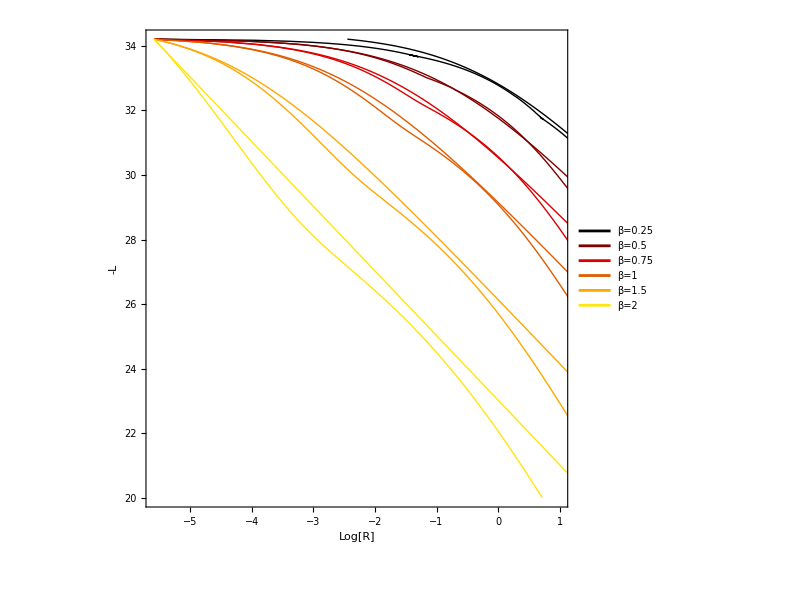

```mathematica
plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->600,AspectRatio->1};
ListLinePlot[{dat00,dat10,dat20,dat30,dat40,dat50,dat01,dat11,dat21,dat31,dat41,dat51},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05]},PlotRange->{{Rref1,1},{fref1,20}},PlotLegends->Placed[{Style["β=0.25",Black],Style["β=0.5",Black],Style["β=0.75",Black],Style["β=1",Black],Style["β=1.5",Black],Style["β=2",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L",Black,28]}]
```

#### log (R) match, L match

```mathematica
(*log(R) match, L match*)
```

```mathematica
k=5;
num = 200;
β0 = 0.5;
β1 =1;
β2=1.5;
β3=2;
β4=2.5;
β5=3;
β6=3.5;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[A_] := 1/√(1);

eps = 0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax}])/norm[Avar]
R[Avar_,kvar_,ϵbarvar_,βvar_] := (NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}])/norm[Avar]

Rref1=Log[R[0,k,var^(β3/2),β3]]
fref1 = -f[0,k,var^(β3/2),β3]

Rref2=Log[R[0,k,var2^(β3/2),β3]]
fref2 =- f[0,k,var2^(β3/2),β3]


Δf0 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β0/2),β0];
ΔR0 =Log[R[0,k,var^(β3/2),β3]]- Log[R[0,k,var^(β0/2),β0]];

Δf1 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β1/2),β1];
ΔR1 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[0,k,var^(β1/2),β1]];

Δf2 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β2/2),β2];
ΔR2 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[0,k,var^(β2/2),β2]];

Δf3 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β3/2),β3];
ΔR3 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[0,k,var^(β3/2),β3]];

Δf4 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β4/2),β4];
ΔR4 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[0,k,var^(β4/2),β4]];

Δf5 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β5/2),β5];
ΔR5 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[0,k,var^(β5/2),β5]];

Δf6 =+f[0,k,var^(β3/2),β3]-f[0,k,var^(β6/2),β6];
ΔR6 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[0,k,var^(β6/2),β6]];

dat00= {};
dat10 = {};
dat20 = {};
dat30 = {};
dat40 = {};
dat50 = {};
dat60 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat00,{Log[R[0,k,lz[[i]]^(β0/2),β0]]+ ΔR0,-(f[0,k,lz[[i]]^(β0/2),β0]+Δf0)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat10,{Log[R[0,k,lz[[i]]^(β1/2),β1]] + ΔR1,-(f[0,k,lz[[i]]^(β1/2),β1]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat20,{Log[R[0,k,lz[[i]]^(β2/2),β2]]+ ΔR2 ,-(f[0,k,lz[[i]]^(β2/2),β2]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat30,{Log[R[0,k,lz[[i]]^(β3/2),β3]]+ ΔR3 ,-(f[0,k,lz[[i]]^(β3/2),β3]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat40,{Log[R[0,k,lz[[i]]^(β4/2),β4]] + ΔR4,-(f[0,k,lz[[i]]^(β4/2),β4]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat50,{Log[R[0,k,lz[[i]]^(β5/2),β5]] + ΔR5,-(f[0,k,lz[[i]]^(β5/2),β5]+Δf5)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat60,{Log[R[0,k,lz[[i]]^(β6/2),β6]]+ ΔR6 ,-(f[0,k,lz[[i]]^(β6/2),β6]+Δf6)}]
]
```

-5.59004

24.9956

6.97633

-0.137154

```mathematica
k=5;
num = 200;
β0 = 0.5;
β1 =1;
β2=1.5;
β3=2;
β4=2.5;
β5=3;
β6=3.5;
A = 0.6;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[A_] := 1/√(1+A);

eps = 0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax}])/norm[Avar]
R[Avar_,kvar_,ϵbarvar_,βvar_] := (NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}])/norm[Avar]

Δf0 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β0/2),β0];
ΔR0 =Log[R[0,k,var^(β3/2),β3]]- Log[R[A,k,var^(β0/2),β0]];

Δf1 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β1/2),β1];
ΔR1 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[A,k,var^(β1/2),β1]];

Δf2 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β2/2),β2];
ΔR2 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[A,k,var^(β2/2),β2]];

Δf3 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β3/2),β3];
ΔR3 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[A,k,var^(β3/2),β3]];

Δf4 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β4/2),β4];
ΔR4 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[A,k,var^(β4/2),β4]];

Δf5 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β5/2),β5];
ΔR5 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[A,k,var^(β5/2),β5]];

Δf6 =+f[0,k,var^(β3/2),β3]-f[A,k,var^(β6/2),β6];
ΔR6 =+Log[R[0,k,var^(β3/2),β3]]- Log[R[A,k,var^(β6/2),β6]];

dat01= {};
dat11 = {};
dat21 = {};
dat31 = {};
dat41 = {};
dat51 = {};
dat61 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat01,{Log[R[A,k,lz[[i]]^(β0/2),β0]]+ ΔR0,-(f[A,k,lz[[i]]^(β0/2),β0]+Δf0)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat11,{Log[R[A,k,lz[[i]]^(β1/2),β1]] + ΔR1,-(f[A,k,lz[[i]]^(β1/2),β1]+Δf1)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat21,{Log[R[A,k,lz[[i]]^(β2/2),β2]]+ ΔR2 ,-(f[A,k,lz[[i]]^(β2/2),β2]+Δf2)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat31,{Log[R[A,k,lz[[i]]^(β3/2),β3]]+ ΔR3 ,-(f[A,k,lz[[i]]^(β3/2),β3]+Δf3)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat41,{Log[R[A,k,lz[[i]]^(β4/2),β4]] + ΔR4,-(f[A,k,lz[[i]]^(β4/2),β4]+Δf4)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat51,{Log[R[A,k,lz[[i]]^(β5/2),β5]] + ΔR5,-(f[A,k,lz[[i]]^(β5/2),β5]+Δf5)}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat61,{Log[R[A,k,lz[[i]]^(β6/2),β6]]+ ΔR6 ,-(f[A,k,lz[[i]]^(β6/2),β6]+Δf6)}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {1.02505}. NIntegrate obtained 16.5361 and 0.0210325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.244196}. NIntegrate obtained 19.5986 and 0.000135306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0570675}. NIntegrate obtained 25.6593 and 1.62174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.00423749}. NIntegrate obtained 28.8881 and 0.238024 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.00392998}. NIntegrate obtained 31.7096 and 0.196639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {1.02505}. NIntegrate obtained 16.5361 and 0.0210325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {1.02833}. NIntegrate obtained 16.4965 and 0.020375 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {1.03167}. NIntegrate obtained 16.4577 and 0.0160425 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.244196}. NIntegrate obtained 19.5986 and 0.000135306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.135509}. NIntegrate obtained 19.5193 and 0.000106467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.136932}. NIntegrate obtained 19.4415 and 0.0000686416 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.068928}. NIntegrate obtained 21.9084 and 0.552045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0695904}. NIntegrate obtained 21.8441 and 0.548423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0702847}. NIntegrate obtained 21.7806 and 0.541245 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0570675}. NIntegrate obtained 25.6593 and 1.62174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.810797}. NIntegrate obtained 26.2304 and 0.213546 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0574548}. NIntegrate obtained 25.1732 and 1.60203 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.00423749}. NIntegrate obtained 28.8881 and 0.238024 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.0042692}. NIntegrate obtained 28.6906 and 0.226177 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.00430351}. NIntegrate obtained 28.4972 and 0.209786 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.00392998}. NIntegrate obtained 31.7096 and 0.196639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.00393796}. NIntegrate obtained 31.4697 and 0.176608 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.00394672}. NIntegrate obtained 31.2344 and 0.162028 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000488632}. NIntegrate obtained 33.7908 and 0.00217534 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000492011}. NIntegrate obtained 33.5815 and 0.00230655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϵ near {ϵ} = {0.000495783}. NIntegrate obtained 33.3939 and 0.0023407 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

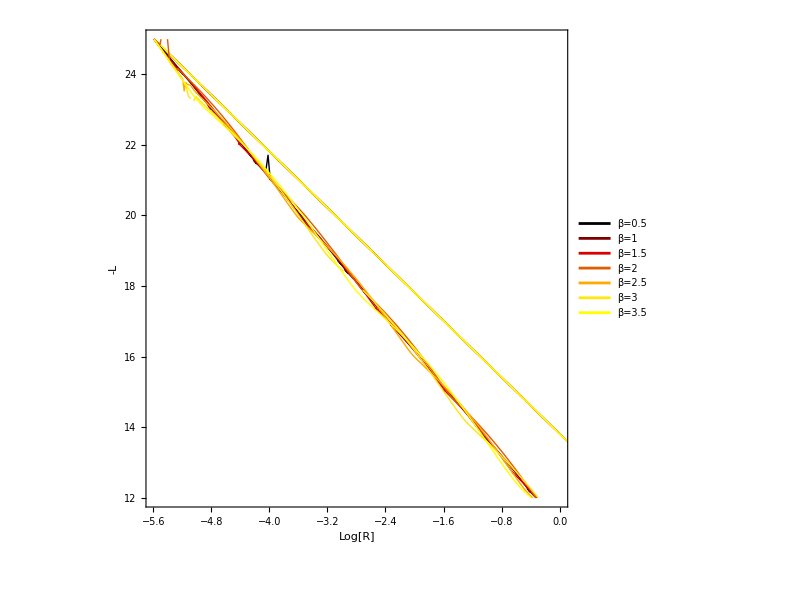

```mathematica
plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->600,AspectRatio->1};
ListLinePlot[{dat00,dat10,dat20,dat30,dat40,dat50,dat60,dat01,dat11,dat21,dat31,dat41,dat51,dat61},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05],RGBColor[1,1,0]},PlotRange->{{Rref1,0},{fref1,12}},PlotLegends->Placed[{Style["β=0.5",Black],Style["β=1",Black],Style["β=1.5",Black],Style["β=2",Black],Style["β=2.5",Black],Style["β=3",Black],Style["β=3.5",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L",Black,28]}]
```

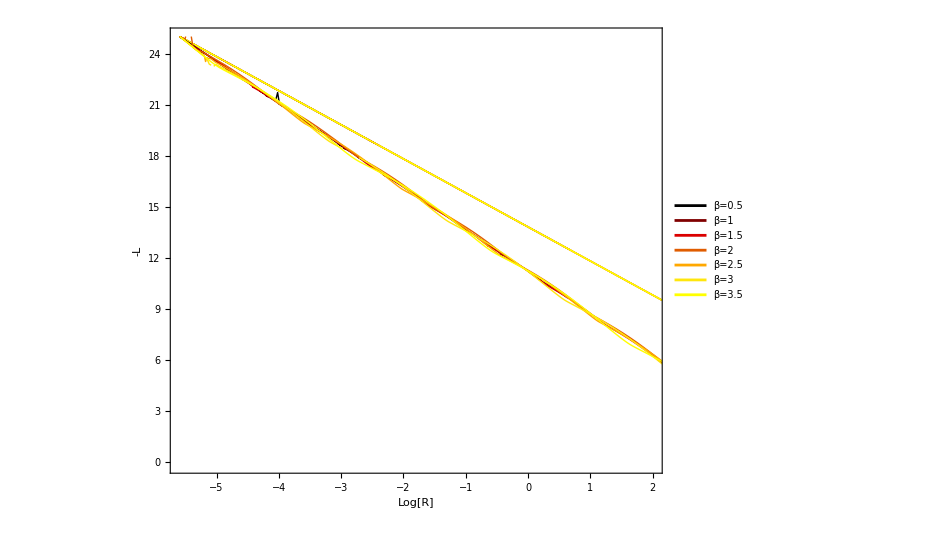

```mathematica
plotOptions={Frame->True,FrameStyle->Directive[18,Thickness[0.004]],LabelStyle->{FontSize->22,FontFamily->"Times",Black,Bold,SingleLetterItalics->False},RotateLabel->False,BaseStyle->{Thick,FontSize->14},AxesStyle->{Thick},FrameTicksStyle->Black,ImageSize->700,AspectRatio->0.8};
ListLinePlot[{dat00,dat10,dat20,dat30,dat40,dat50,dat60,dat01,dat11,dat21,dat31,dat41,dat51,dat61},Evaluate[plotOptions],PlotStyle-> {RGBColor[0,0,0],RGBColor[0.5,0,0],RGBColor[0.86,0,0],RGBColor[0.88,0.36,0],RGBColor[1,0.66,0],RGBColor[1,0.9,0.05],RGBColor[1,1,0]},PlotRange->{{Rref1,2},{fref1,fref2}},PlotLegends->Placed[{Style["β=0.5",Black],Style["β=1",Black],Style["β=1.5",Black],Style["β=2",Black],Style["β=2.5",Black],Style["β=3",Black],Style["β=3.5",Black]},{0.20,0.60}],FrameLabel->{Style["Log[R]",Black,22,SingleLetterItalics->False],Style["-L",Black,28]}]
```

#### R LogL match

```mathematica
k=5;
num = 200;
β0 = 0.5;
β1 =1;
β2=1.5;
β3=2;
β4=2.5;
β5=3;
β6=3.5;
n1=-k;
n2=k;
A=0;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[Avar_] := 1/√(1+Avar);

eps = 0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax}])/norm[Avar]
R[Avar_,kvar_,ϵbarvar_,βvar_] := (NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}] )/norm[Avar]

Rref1=Log[R[0,k,var^(β3/2),β3]]
fref1 = -f[0,k,var^(β3/2),β3]

Rref2=Log[R[0,k,var2^(β3/2),β3]]
fref2 =- f[0,k,var2^(β3/2),β3]

Δf0 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[0,k,var^(β0/2),β0]];
ΔR0 =R[0,k,var^(β3/2),β3]-R[0,k,var^(β0/2),β0];

Δf1 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[0,k,var^(β1/2),β1]];
ΔR1 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β1/2),β1];

Δf2 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[0,k,var^(β2/2),β2]];
ΔR2 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β2/2),β2];

Δf3 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[0,k,var^(β3/2),β3]];
ΔR3 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β3/2),β3];

Δf4 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[0,k,var^(β4/2),β4]];
ΔR4 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β4/2),β4];

Δf5 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[0,k,var^(β5/2),β5]];
ΔR5 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β5/2),β5];

Δf6 =+Log[ f[0,k,var^(β3/2),β3]]-Log[f[0,k,var^(β6/2),β6]];
ΔR6 =R[0,k,var^(β3/2),β3]- R[0,k,var^(β6/2),β6];

dat00 = {};
dat10 = {};
dat20 = {};
dat30 = {};
dat40 = {};
dat50 = {};
dat60 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat00,{Log[R[0,k,lz[[i]]^(β0/2),β0]+ ΔR0],-(f[0,k,lz[[i]]^(β0/2),β0]*Exp[Δf0])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat10,{Log[R[0,k,lz[[i]]^(β1/2),β1]+ ΔR1] ,-(f[0,k,lz[[i]]^(β1/2),β1]*Exp[Δf1])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat20,{Log[R[0,k,lz[[i]]^(β2/2),β2]+ ΔR2] ,-(f[0,k,lz[[i]]^(β2/2),β2]*Exp[Δf2])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat30,{Log[R[0,k,lz[[i]]^(β3/2),β3]+ ΔR3] ,-(f[0,k,lz[[i]]^(β3/2),β3]*Exp[Δf3])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat40,{Log[R[0,k,lz[[i]]^(β4/2),β4]+ ΔR4] ,-(f[0,k,lz[[i]]^(β4/2),β4]*Exp[Δf4])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat50,{Log[R[0,k,lz[[i]]^(β5/2),β5]+ ΔR5] ,-(f[0,k,lz[[i]]^(β5/2),β5]*Exp[Δf5])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat60,{Log[R[0,k,lz[[i]]^(β6/2),β6]+ ΔR6] ,-(f[0,k,lz[[i]]^(β6/2),β6]*Exp[Δf6])}]
]
```

```mathematica
k=5;
num = 200;
β0 = 0.5;
β1 =1;
β2=1.5;
β3=2;
β4=2.5;
β5=3;
β6=3.5;
A = 0.6;
n1=-k;
n2=k;
var = Exp[2π*n1/k];
var2 =  Exp[2π*n2/k];
norm[A_] := 1/√(1+A);

eps = 0;
epsmax = 1000;
f[Avar_,kvar_,ϵbarvar_,βvar_]:=(NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]*(1/Sqrt[(ϵbarvar/ϵ)^2-1]*ϵbarvar/ϵ^2-1/ϵ),{ϵ,eps,ϵbarvar}]-NIntegrate[2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])]/ϵ,{ϵ,ϵbarvar,epsmax}])/norm[Avar]
R[Avar_,kvar_,ϵbarvar_,βvar_] := (NIntegrate[ 2*Sqrt[(1+Avar*Cos[2*kvar/βvar*Log[ϵ]])/((ϵbarvar/ϵ)^2-1)],{ϵ,eps,ϵbarvar}])/norm[Avar]

Δf0 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[A,k,var^(β0/2),β0]];
ΔR0 =R[0,k,var^(β3/2),β3]-R[A,k,var^(β0/2),β0];

Δf1 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[A,k,var^(β1/2),β1]];
ΔR1 =R[0,k,var^(β3/2),β3]- R[A,k,var^(β1/2),β1];

Δf2 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[A,k,var^(β2/2),β2]];
ΔR2 =R[0,k,var^(β3/2),β3]- R[A,k,var^(β2/2),β2];

Δf3 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[A,k,var^(β3/2),β3]];
ΔR3 =R[0,k,var^(β3/2),β3]- R[A,k,var^(β3/2),β3];

Δf4 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[A,k,var^(β4/2),β4]];
ΔR4 =R[0,k,var^(β3/2),β3]- R[A,k,var^(β4/2),β4];

Δf5 =+Log[f[0,k,var^(β3/2),β3]]-Log[f[A,k,var^(β5/2),β5]];
ΔR5 =R[0,k,var^(β3/2),β3]- R[A,k,var^(β5/2),β5];

Δf6 =+Log[ f[0,k,var^(β3/2),β3]]-Log[f[A,k,var^(β6/2),β6]];
ΔR6 =R[0,k,var^(β3/2),β3]- R[A,k,var^(β6/2),β6];

dat01= {};
dat11 = {};
dat21 = {};
dat31 = {};
dat41 = {};
dat51 = {};
dat61 = {};

(*Table[i,{i,var,var2,(var2-var)/10000}];*)
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat01,{Log[R[A,k,lz[[i]]^(β0/2),β0]+ ΔR0],-(f[A,k,lz[[i]]^(β0/2),β0]*Exp[Δf0])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat11,{Log[R[A,k,lz[[i]]^(β1/2),β1]+ ΔR1] ,-(f[A,k,lz[[i]]^(β1/2),β1]*Exp[Δf1])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat21,{Log[R[A,k,lz[[i]]^(β2/2),β2]+ ΔR2] ,-(f[A,k,lz[[i]]^(β2/2),β2]*Exp[Δf2])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat31,{Log[R[A,k,lz[[i]]^(β3/2),β3]+ ΔR3] ,-(f[A,k,lz[[i]]^(β3/2),β3]*Exp[Δf3])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat41,{Log[R[A,k,lz[[i]]^(β4/2),β4]+ ΔR4] ,-(f[A,k,lz[[i]]^(β4/2),β4]*Exp[Δf4])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat51,{Log[R[A,k,lz[[i]]^(β5/2),β5]+ ΔR5] ,-(f[A,k,lz[[i]]^(β5/2),β5]*Exp[Δf5])}]
]
lz = Table[Exp[i*2π/k],{i,n1,n2,(n2-n1)/num}];
For[i=1,i<Dimensions[lz][[1]],i++,
AppendTo[dat61,{Log[R[A,k,lz[[i]]^(β6/2),β6]+ ΔR6] ,-(f[A,k,lz[[i]]^(β6/2),β6]*Exp[Δf6])}]
]
```

### Lifshitz:

```mathematica
f[t_,x_,z_] = 1/(t^z+x^2);
```

```mathematica
Plot3D[Log[f[y,Exp[x],3]],{x,0,10},{y,-1,10}]
```

-Graphics3D-

### Corr for Gaussian dist:

```mathematica
Integrate[1/(x0-x)*Exp[-(x-x0)^2/(4*D*t)],{x,0,∞}]
```

Integrate::idiv: Integral of -(1. ⅇ^(-(0.00025 (-«22»+x)^2)/D))/(-0.00373489+x) does not converge on {0,∞}.

∫_0^∞ (ⅇ^(-(-0.00373489+x)^2/(4000 D)))/(0.00373489-x)ⅆx

```mathematica
Log[-2 D ⅇ^(-x0^2/(4 D t)) t] // Simplify
```

Log[-2 D ⅇ^(-x0^2/(4 D t)) t]

```mathematica
Logcorr[x_,D_,t_] = +1/x
```

1/x

```mathematica
First[dat01]
 Last[dat01]
```

{-5.59004,24.9956}

{3.20386,15.2911}

1000

1000

1000

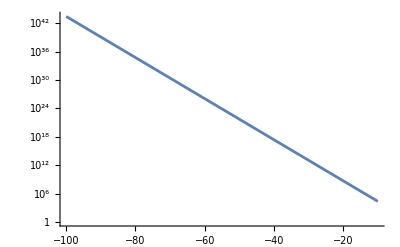

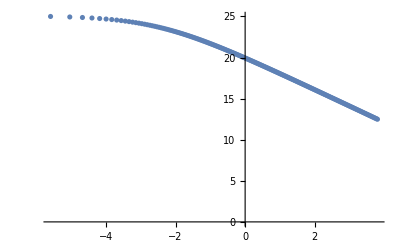

```mathematica
var = 1000
t = 1000
Ds=1000

Show[LogPlot[Logcorr[Exp[x],Ds,t],{x,-100, -10}]
]
ListPlot[dat10]
```